# INTSECA

This notebook contains details of using twisted intersection theory to generate the master integrals and the associated canonical system for the single massive exchange diagram in FRW cosmology.

```mathematica
SetDirectory[NotebookDirectory[]];
<<INTSECA.wl
```

INTSECA 1.2.3

## single massive exchange (dS)

### Definitions

```mathematica
dim=4;
nkin=3;
kin={X1,X2,Y};
```

Untwisted hyperplanes:

```mathematica
nBplane=4;
B[1]={1,0,Y,0,X1+Y};
B[2]={0,1,0,Y,X2+Y};
B[3]={1,1,Y,-Y,X1+X2};
B[4]={1,1,-Y,Y,X1+X2};
```

Set Y=1 since we can absorb Y into X1, X2.

Twisted hyperplanes:

```mathematica
nTplane=6;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,1,0,2};
T[5]={0,0,0,1,0};
T[6]={0,0,0,1,2};
powers={-e,-e,e,e,e,e};
twists={e};
```

two twists, one for mass and the other for FRW

Wavefunction:

let’s deal with the inhomogeneous part: (anti-)time-ordered

```mathematica
psi=⟨1,3,5,6⟩-⟨2,4,5,6⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

116

```mathematica
verticesList
```

{⟨1,2,3,4⟩,⟨1,2,3,5⟩,⟨1,2,3,7⟩,⟨1,2,3,8⟩,⟨1,2,4,6⟩,⟨1,2,4,9⟩,⟨1,2,4,10⟩,⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,5,10⟩,⟨1,2,6,7⟩,⟨1,2,6,8⟩,⟨1,2,7,9⟩,⟨1,2,7,10⟩,⟨1,2,8,9⟩,⟨1,2,8,10⟩,⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩,⟨1,3,4,10⟩,⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,5,10⟩,⟨1,3,6,7⟩,⟨1,3,6,8⟩,⟨1,3,7,9⟩,⟨1,3,7,10⟩,⟨1,3,8,9⟩,⟨1,3,8,10⟩,⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,5,10⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,6,10⟩,⟨1,4,7,9⟩,⟨1,4,7,10⟩,⟨1,4,8,9⟩,⟨1,4,8,10⟩,⟨1,5,6,9⟩,⟨1,5,6,10⟩,⟨1,6,7,9⟩,⟨1,6,7,10⟩,⟨1,6,8,9⟩,⟨1,6,8,10⟩,⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩,⟨2,3,4,10⟩,⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,5,10⟩,⟨2,3,6,7⟩,⟨2,3,6,8⟩,⟨2,3,7,9⟩,⟨2,3,7,10⟩,⟨2,3,8,9⟩,⟨2,3,8,10⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,5,10⟩,⟨2,4,6,7⟩,⟨2,4,6,8⟩,⟨2,4,7,9⟩,⟨2,4,7,10⟩,⟨2,4,8,9⟩,⟨2,4,8,10⟩,⟨2,5,6,7⟩,⟨2,5,6,8⟩,⟨2,5,7,9⟩,⟨2,5,7,10⟩,⟨2,5,8,9⟩,⟨2,5,8,10⟩,⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩,⟨3,4,5,10⟩,⟨3,4,6,7⟩,⟨3,4,6,8⟩,⟨3,4,6,9⟩,⟨3,4,6,10⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,6,10⟩,⟨3,5,7,9⟩,⟨3,5,7,10⟩,⟨3,5,8,9⟩,⟨3,5,8,10⟩,⟨3,6,7,9⟩,⟨3,6,7,10⟩,⟨3,6,8,9⟩,⟨3,6,8,10⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,6,10⟩,⟨4,5,7,9⟩,⟨4,5,7,10⟩,⟨4,5,8,9⟩,⟨4,5,8,10⟩,⟨4,6,7,9⟩,⟨4,6,7,10⟩,⟨4,6,8,9⟩,⟨4,6,8,10⟩,⟨5,6,7,9⟩,⟨5,6,7,10⟩,⟨5,6,8,9⟩,⟨5,6,8,10⟩}

```mathematica
sol=Sol[0];
```

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({3} | {⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩}
{4} | {⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}
{1,2} | {⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩}
{1,3} | {⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩}
{1,4} | {⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩}
{2,3} | {⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩}
{2,4} | {⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩}
{3,4} | {⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩}
{1,2,3} | {⟨1,2,3,5⟩,⟨1,2,3,7⟩}
{1,2,4} | {⟨1,2,4,6⟩,⟨1,2,4,9⟩}
{1,3,4} | {⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩}
{2,3,4} | {⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩}
{1,2,3,4} | {⟨1,2,3,4⟩})

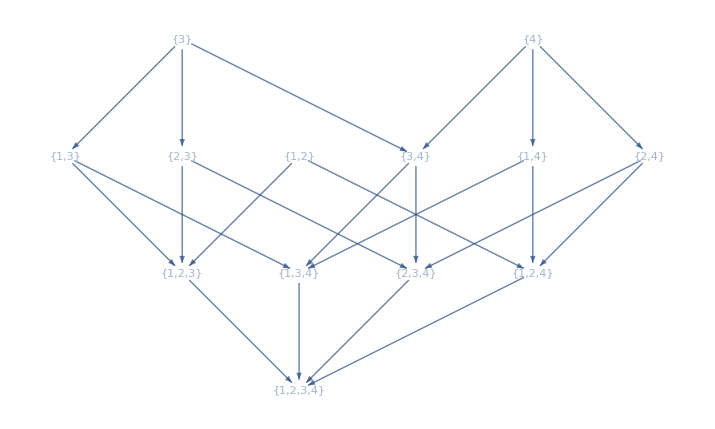

# codimension | 0 | 1 | 2 | 3 | 4
# boundaries | 0 | 2 | 6 | 4 | 1

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

```mathematica
basis=bdyBasis[[2]]//Flatten;
```

```mathematica
basis//Length
```

50

```mathematica
EchoTiming[A0 = AMatrix[0]];
A0[[1]] // MatrixPlot
```

11.3547

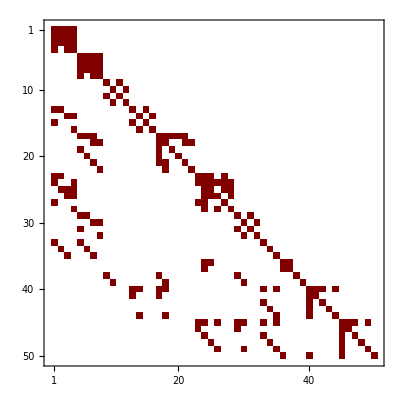

### Basis reduction: filtering

#### start

The stored A-matrix from previous overcomplete set of basis functions:

ClearAll[basis, A0, A];
Get[FileNameJoin[{NotebookDirectory[], "storage", "basis_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A0_single-massive-exchange"}]];

basis // Length
A0[[1]] // Length
A[[1]] // Length

50

50

44

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(e (Log[X1+X2]-3 Log[Y]) | e (-Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-3 Log[Y]) | e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (Log[Y]-Log[X1+X2+2 Y]) | e (Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X1+Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-2 Log[Y]+Log[X1+Y]-Log[X2+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (-2 Log[Y]-Log[X1+Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+Y]+Log[X2+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[-2 X1-X2-Y]+Log[2 X1+X2-Y]) | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[Y]) | e (-Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | 0 | e (Log[X2-3 Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | e (Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y]) | e (Log[X2-3 Y]-Log[Y]) | e (Log[X2-3 Y]-Log[X2-Y]) | e (-Log[X2-3 Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y]) | 0 | e (Log[X2+Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[X2+3 Y]) | e (Log[X2-Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[Y]) | e (Log[-2 X1-X2-Y]-Log[X2+3 Y]) | e (-Log[X2-Y]+Log[Y]) | e (Log[Y]-Log[X2+3 Y]) | e (-Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y]) | e (-Log[X2-Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2-Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2-Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1+2 X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (-Log[Y]+Log[X1+3 Y]) | e (-Log[X1-Y]+Log[X1+3 Y]) | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1+2 X2-Y]-Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y]) | 0 | e (-Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-3 Y]+Log[X2+Y]) | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[Y]) | e (-Log[X1-3 Y]+Log[Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X2-Y]-Log[X1+2 X2+Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | e (-2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (-Log[X2-Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-4 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (-Log[X1-Y]-2 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | 0 | e Log[Y] | e (Log[X1+X2]-Log[Y]) | 0 | 0 | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e Log[X1+X2] | -e Log[Y] | e Log[Y] | 0 | e Log[X1+X2] | e Log[Y] | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[Y] | e (-2 Log[X1+X2]-2 Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1+X2]+Log[Y]) | -e Log[Y] | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[Y] | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]-2 Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]-2 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | e (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y]) | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | e (-Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | -e Log[Y] | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | 0 | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2+Y] | e Log[Y] | -e Log[X2+Y] | -e Log[Y] | 0 | -e Log[Y] | 0 | -e Log[X2+Y] | -e Log[Y] | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | e Log[X1-Y] | e Log[X2+Y] | -e Log[Y] | e (-Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | e Log[Y] | 0 | e (Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e Log[Y] | 0 | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y]) | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | e (-Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | -e Log[Y] | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e Log[Y] | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0 | e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2-Y] | 0 | e Log[X1+Y] | e Log[Y] | -e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | e Log[Y] | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+Y] | e Log[X2-Y] | -e Log[Y] | e (-Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | -e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | e Log[Y] | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | -e Log[Y] | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e Log[Y] | 0 | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | e (-Log[X2]+Log[Y]) | 0 | e (Log[X1]-Log[Y]) | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (-Log[X1]-Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{X1,X2,X1+X2,X1-3 Y,X2-3 Y,X1+X2-2 Y,X1-Y,-2 X1-X2-Y,X2-Y,2 X1+X2-Y,X1+2 X2-Y,Y,X1+Y,X2+Y,X1+2 X2+Y,X1+X2+2 Y,X1+3 Y,X2+3 Y}

18

```mathematica
Coefficient[Amatrix,e]//MatrixForm
```

(Log[X1+X2]-3 Log[Y] | -Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2]-Log[Y] | Log[X1+X2-2 Y]-3 Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | -Log[X1+X2-2 Y]+Log[Y] | Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y] | -2 Log[X1+X2]+2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-3 Log[Y] | Log[X1+X2-2 Y]-Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | -3 Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | Log[Y]-Log[X1+X2+2 Y] | Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y] | -2 Log[X1+X2]+2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X1+Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -2 Log[Y]+Log[X1+Y]-Log[X2+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | -2 Log[Y]-Log[X1+Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[Y]-Log[X2+Y] | -Log[X1+Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+Y]-Log[X2+Y] | Log[X1-Y]-Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-Y]+Log[X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+Y]+Log[X2+Y] | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | Log[X2-Y]-2 Log[Y]-Log[X1+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[-2 X1-X2-Y]+Log[2 X1+X2-Y] | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-2 X1-X2-Y]-Log[Y] | -Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | 0 | Log[X2-3 Y]-Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y] | Log[X2-3 Y]-Log[Y] | Log[X2-3 Y]-Log[X2-Y] | -Log[X2-3 Y]+Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | Log[X2+Y]-Log[X2+3 Y] | -Log[X2+Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | -Log[X2+Y]+Log[X2+3 Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y] | 0 | Log[X2+Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[X2+3 Y] | Log[X2-Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[Y] | Log[-2 X1-X2-Y]-Log[X2+3 Y] | -Log[X2-Y]+Log[Y] | Log[Y]-Log[X2+3 Y] | -Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y] | -Log[X2-Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X2-Y]+Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2-Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2-Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1+2 X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+2 X2+Y]-Log[X1+3 Y] | 0 | 0 | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y] | -Log[Y]+Log[X1+3 Y] | -Log[X1-Y]+Log[X1+3 Y] | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Log[X1+2 X2-Y]-Log[X1+Y] | Log[X1-3 Y]-Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y] | 0 | -Log[X1+2 X2-Y]+Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-3 Y]+Log[X2+Y] | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1-Y]+Log[Y] | -Log[X1-3 Y]+Log[Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X2-Y]-Log[X1+2 X2+Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | -2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | -Log[X2-Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-4 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2-Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[X1-Y]-2 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | 0 | Log[Y] | Log[X1+X2]-Log[Y] | 0 | 0 | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2]-Log[Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[X1+X2] | -Log[Y] | Log[Y] | 0 | Log[X1+X2] | Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y] | -2 Log[X1+X2]-2 Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1+X2]+Log[Y] | -Log[Y] | 0 | 0 | Log[X1+X2]-Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y] | 0 | -2 Log[X1+X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | -Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]-2 Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[X2-Y] | 0 | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]-2 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y] | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | -Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | 0 | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2+Y] | Log[Y] | -Log[X2+Y] | -Log[Y] | 0 | -Log[Y] | 0 | -Log[X2+Y] | -Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | Log[X1-Y] | Log[X2+Y] | -Log[Y] | -Log[X1-Y]-2 Log[Y]-Log[X2+Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | Log[Y] | 0 | Log[Y]-Log[X1+Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | Log[Y] | 0 | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y] | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2-Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | -Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | Log[Y] | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0 | Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y] | 0 | Log[X1+Y] | Log[Y] | -Log[X2-Y] | -Log[Y] | Log[X2-Y] | -Log[Y] | Log[X2-Y] | Log[Y] | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+Y] | Log[X2-Y] | -Log[Y] | -Log[X2-Y]-2 Log[Y]-Log[X1+Y] | -Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | Log[Y] | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[Y] | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | Log[Y] | 0 | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | -Log[X2]+Log[Y] | 0 | Log[X1]-Log[Y] | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X1]+Log[Y] | -Log[X2]+Log[Y] | 0 | 0 | 0 | -Log[X1]-Log[X2])

we can pick

```mathematica
need=Position[basis,#]&/@(Join[
{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩},
{⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩},
{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩},
{⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}])//Flatten
```

{13,14,15,16,29,30,31,32,1,2,3,4,5,6,7,8}

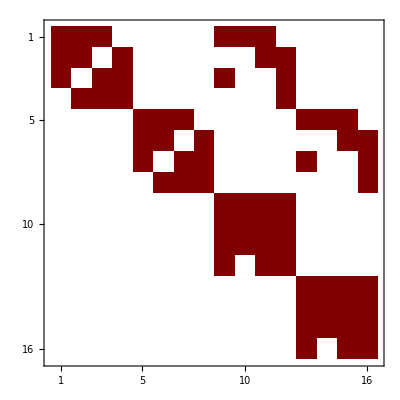

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->Coefficient[AmatrixNeed,e].basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y],Log[Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩,-4 ⟨1,3,5,6⟩+4 ⟨2,4,5,6⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | -⟨3,5,6,7⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,7⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | ⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩)

{⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

5

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

20

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,False,False,True,False,True,True,True,False,True,False,False,True,True,True,True,False,False,True,False}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

6

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

{{{2},{17}}}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

14

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

6

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

8

6 = 1 + (2+1) + (1+1)
8 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_13
φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15
φ_1+φ_3+φ_7+φ_9-φ_14
φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16
φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_5

so psi is just the new basis 1.

### A matrix (associated to physical basis)

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basisNeed[[j]]],{i,1,Length[Basis]},{j,1,Length[basisNeed]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Amatrix6=Umatrix.AmatrixNeed.Uinv//Simplify;
%//MatrixForm
```

(2 e (-2 Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0
e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]+Log[X2-Y]-Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y])
e (Log[X1+X2-2 Y]-Log[X1-Y]-2 Log[Y]+2 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1-Y]+Log[X1+Y])
e (Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | 0 | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2]-Log[X2-Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X2-Y]-Log[X2+Y])
-e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | 0 | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | -e (Log[X1+X2-2 Y]+Log[X1+X2+2 Y]) | 0
e (-Log[X1-Y]+Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]) | e (Log[X1-Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | -e (Log[X1-Y]+Log[X2+Y]))

{1,2,3} {4,5} {6,7,8}
notice that l7, l8 are suspicious poles. To eliminate the spurious poles, we may further reduce the size. (there is further redundancy in the integral repr. of Hankel function)
6 = 1 + (2+1) + (1+1)

```mathematica
lett=Join[l0,Complement[l1,l0],Complement[l2,l1]]
```

{Log[X1+Y],Log[X2+Y],Log[Y],Log[X1-Y],Log[X2-Y],Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

the matrix is not upper triangular...

```mathematica
A6=Coefficient[Amatrix6,e]/. Thread[lett->Table[ToExpression["L"<>ToString[i]],{i,1,Length[letters]}]]//Simplify
```

{{2 (L2-2 L3),-L2+L4,-L2+L5,L1-L2,0,0},{L2-L7,-3 L3+L7,-L2+L5,L1-L2-L3+L7,-L2+L5+L6-L7,L2-L5},{2 L2-2 L3-L4+L7,-L2+L3+L4-L7,-L2-2 L3+L4,-L2+L3+L4-L7,-L6+L7,L1-L4},{L2-L8,-L2-L3+L4+L8,0,-3 L3+L8,L2-L5+L6-L8,-L2+L5},{2 L3-L7-L8,-2 L3+L7+L8,0,-2 L3+L7+L8,-L7-L8,0},{L2+L3-L4-L8,-L2-L3+L4+L8,-L3+L4,-2 L3+L4+L8,L2-L8,-L2-L4}}

```mathematica
%//MatrixForm
```

(2 (L2-2 L3) | -L2+L4 | -L2+L5 | L1-L2 | 0 | 0
L2-L7 | -3 L3+L7 | -L2+L5 | L1-L2-L3+L7 | -L2+L5+L6-L7 | L2-L5
2 L2-2 L3-L4+L7 | -L2+L3+L4-L7 | -L2-2 L3+L4 | -L2+L3+L4-L7 | -L6+L7 | L1-L4
L2-L8 | -L2-L3+L4+L8 | 0 | -3 L3+L8 | L2-L5+L6-L8 | -L2+L5
2 L3-L7-L8 | -2 L3+L7+L8 | 0 | -2 L3+L7+L8 | -L7-L8 | 0
L2+L3-L4-L8 | -L2-L3+L4+L8 | -L3+L4 | -2 L3+L4+L8 | L2-L8 | -L2-L4)

#### check flatness

```mathematica
Amatrix6//MatrixForm
```

(2 e (-2 Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+Y]-Log[X2+Y]) | 0 | 0
e (-Log[X1+X2-2 Y]+Log[X2+Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1+X2-2 Y]-Log[Y]+Log[X1+Y]-Log[X2+Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]+Log[X2-Y]-Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y])
e (Log[X1+X2-2 Y]-Log[X1-Y]-2 Log[Y]+2 Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | e (-Log[X1+X2-2 Y]+Log[X1-Y]+Log[Y]-Log[X2+Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (-Log[X1-Y]+Log[X1+Y])
e (Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | 0 | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2]-Log[X2-Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X2-Y]-Log[X2+Y])
-e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | 0 | e (Log[X1+X2-2 Y]-2 Log[Y]+Log[X1+X2+2 Y]) | -e (Log[X1+X2-2 Y]+Log[X1+X2+2 Y]) | 0
e (-Log[X1-Y]+Log[Y]+Log[X2+Y]-Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]-Log[X2+Y]+Log[X1+X2+2 Y]) | e (Log[X1-Y]-Log[Y]) | e (Log[X1-Y]-2 Log[Y]+Log[X1+X2+2 Y]) | e (Log[X2+Y]-Log[X1+X2+2 Y]) | -e (Log[X1-Y]+Log[X2+Y]))

```mathematica
Amatrix6;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

#### DEQ

can we directly derive the PDE with the above 6x6 A-matrix?

we need to also convert the ODE to PDE.

### Basis reduction: filtering with symmetry condition

#### start

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(e (Log[X1+X2]-3 Log[Y]) | e (-Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+X2]-Log[Y]) | e (Log[X1+X2-2 Y]-3 Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | e (-Log[X1+X2-2 Y]+Log[Y]) | e (Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-3 Log[Y]) | e (Log[X1+X2-2 Y]-Log[Y]) | e (-Log[X1+X2]+Log[X1+X2-2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2-2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e (-3 Log[Y]+Log[X1+X2+2 Y]) | e (-Log[X1+X2]+Log[X1+X2+2 Y]) | e (2 Log[X1+X2]-2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | e (Log[Y]-Log[X1+X2+2 Y]) | e (Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y]) | e (-2 Log[X1+X2]+2 Log[X1+X2+2 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[Y]) | 0 | e (Log[X1+X2]-Log[Y]) | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X1+Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-2 Log[Y]+Log[X1+Y]-Log[X2+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (-2 Log[Y]-Log[X1+Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1+Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+Y]+Log[X2+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+Y]) | 0 | e (Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y]) | e (-Log[-2 X1-X2-Y]+Log[2 X1+X2-Y]) | e (-Log[2 X1+X2-Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[2 X1+X2-Y]) | e (Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-2 X1-X2-Y]-Log[Y]) | e (-Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y]) | 0 | 0 | e (-Log[X1-Y]+Log[-2 X1-X2-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | 0 | e (Log[X2-3 Y]-Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-3 Y]-Log[X1+Y]) | 0 | e (Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y]) | e (Log[X2-3 Y]-Log[Y]) | e (Log[X2-3 Y]-Log[X2-Y]) | e (-Log[X2-3 Y]+Log[X2-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (Log[X2+Y]-Log[X2+3 Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | e (-Log[X2+Y]+Log[X2+3 Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y]) | 0 | e (Log[X2+Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[X2+3 Y]) | e (Log[X2-Y]-Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-2 X1-X2-Y]+Log[Y]) | e (Log[-2 X1-X2-Y]-Log[X2+3 Y]) | e (-Log[X2-Y]+Log[Y]) | e (Log[Y]-Log[X2+3 Y]) | e (-Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y]) | e (-Log[X2-Y]+Log[X2+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X2-Y]+Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2-Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2+Y]) | e (Log[X2-Y]-Log[X1+2 X2-Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (-Log[X1+2 X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y]) | e (-Log[Y]+Log[X1+3 Y]) | e (-Log[X1-Y]+Log[X1+3 Y]) | e (Log[X1+2 X2+Y]-Log[X1+3 Y]) | e (Log[X1-Y]-Log[X1+3 Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (Log[X1+2 X2-Y]-Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y]) | 0 | e (-Log[X1+2 X2-Y]+Log[X1+Y]) | e (-Log[X1-3 Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1-3 Y]+Log[X2+Y]) | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[Y]) | e (-Log[X1-3 Y]+Log[Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (Log[X1-3 Y]-Log[X1-Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[X2-Y]-Log[X1+2 X2+Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X1+2 X2+Y]) | 0 | 0 | e (-2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2-Y]) | e (-Log[X2-Y]+Log[X1+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-4 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+Y]+Log[X2+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2-Y]) | 0 | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | e (-Log[X1-Y]-2 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (Log[Y]-Log[X2+Y]) | e (-Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[X1+X2]+Log[Y]) | 0 | 0 | e Log[Y] | e (Log[X1+X2]-Log[Y]) | 0 | 0 | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e Log[X1+X2] | -e Log[Y] | e Log[Y] | 0 | e Log[X1+X2] | e Log[Y] | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[Y] | e (-2 Log[X1+X2]-2 Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[X1+X2]+Log[Y]) | -e Log[Y] | 0 | 0 | e (Log[X1+X2]-Log[Y]) | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[Y] | 0 | e (-2 Log[X1+X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | e (-Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2]-2 Log[Y]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | 0 | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (-Log[X2]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]-2 Log[Y]+Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | 0 | 0 | e (Log[Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y]) | e (Log[X1+X2]-Log[X1-Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2+Y]) | e (-Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y]) | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X2-Y]-Log[Y]) | -e Log[Y] | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | 0 | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2+Y] | e Log[Y] | -e Log[X2+Y] | -e Log[Y] | 0 | -e Log[Y] | 0 | -e Log[X2+Y] | -e Log[Y] | e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | e Log[X1-Y] | e Log[X2+Y] | -e Log[Y] | e (-Log[X1-Y]-2 Log[Y]-Log[X2+Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | 0 | e Log[Y] | 0 | e (Log[Y]-Log[X1+Y]) | 0 | 0 | e (-Log[X2-Y]+Log[Y]) | -e Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | e (-Log[Y]+Log[X1+Y]) | e (Log[X2-Y]-Log[Y]) | e Log[Y] | 0 | e (-Log[X2-Y]-Log[Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+Log[X1+Y]) | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | e (Log[X1-Y]-Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y]) | e (Log[X1+X2]-Log[X1+Y]) | e (-Log[X1-Y]+Log[X1+Y]) | 0 | e (-Log[X1-Y]+Log[X1+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | 0 | 0 | 0 | e (-Log[X2-Y]+Log[X2+Y]) | 0 | e (-Log[X1+X2]+Log[X2-Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1+X2]-Log[X2-Y]) | e (-Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y]) | e (Log[X2-Y]-Log[X2+Y]) | 0 | e (Log[X2-Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | 0 | e (-Log[Y]+Log[X2+Y]) | -e Log[Y] | 0 | 0 | e (Log[Y]-Log[X2+Y]) | e Log[Y] | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0 | e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2-Y] | 0 | e Log[X1+Y] | e Log[Y] | -e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | -e Log[Y] | e Log[X2-Y] | e Log[Y] | 0 | e (-Log[X2-Y]+Log[X1+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+Y] | e Log[X2-Y] | -e Log[Y] | e (-Log[X2-Y]-2 Log[Y]-Log[X1+Y]) | -e Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | 0 | e Log[Y] | 0 | e (-Log[X1-Y]+Log[Y]) | 0 | -e Log[Y] | 0 | 0 | e (Log[X1-Y]-Log[X2+Y]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1-Y]-Log[Y]) | e (-Log[Y]+Log[X2+Y]) | e Log[Y] | 0 | e (-Log[X1-Y]-Log[Y]-Log[X2+Y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[X1]-Log[Y]) | 0 | e (-Log[X2]+Log[Y]) | 0 | e (Log[X1]-Log[Y]) | e (Log[X2]-Log[Y]) | 0 | 0 | 0 | e (-Log[X1]+Log[Y]) | e (-Log[X2]+Log[Y]) | 0 | 0 | 0 | e (-Log[X1]-Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{X1,X2,X1+X2,X1-3 Y,X2-3 Y,X1+X2-2 Y,X1-Y,-2 X1-X2-Y,X2-Y,2 X1+X2-Y,X1+2 X2-Y,Y,X1+Y,X2+Y,X1+2 X2+Y,X1+X2+2 Y,X1+3 Y,X2+3 Y}

18

```mathematica
Coefficient[Amatrix,e]//MatrixForm
```

(Log[X1+X2]-3 Log[Y] | -Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2]-Log[Y] | Log[X1+X2-2 Y]-3 Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | -Log[X1+X2-2 Y]+Log[Y] | Log[X1+X2]-Log[X1+X2-2 Y]-2 Log[Y] | -2 Log[X1+X2]+2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-3 Log[Y] | Log[X1+X2-2 Y]-Log[Y] | -Log[X1+X2]+Log[X1+X2-2 Y] | 2 Log[X1+X2]-2 Log[X1+X2-2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2]-Log[Y] | -3 Log[Y]+Log[X1+X2+2 Y] | -Log[X1+X2]+Log[X1+X2+2 Y] | 2 Log[X1+X2]-2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | Log[Y]-Log[X1+X2+2 Y] | Log[X1+X2]-2 Log[Y]-Log[X1+X2+2 Y] | -2 Log[X1+X2]+2 Log[X1+X2+2 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2]+Log[Y] | 0 | Log[X1+X2]-Log[Y] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X1+Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -2 Log[Y]+Log[X1+Y]-Log[X2+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | -2 Log[Y]-Log[X1+Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[Y]-Log[X2+Y] | -Log[X1+Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+Y]-Log[X2+Y] | Log[X1-Y]-Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-Y]+Log[X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+Y]+Log[X2+Y] | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+Y] | 0 | Log[X2-Y]-2 Log[Y]-Log[X1+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]+Log[-2 X1-X2-Y]-Log[2 X1+X2-Y]-4 Log[Y]+Log[X1+Y] | -Log[-2 X1-X2-Y]+Log[2 X1+X2-Y] | -Log[2 X1+X2-Y]+Log[X1+Y] | Log[X1-Y]-Log[2 X1+X2-Y] | Log[-2 X1-X2-Y]-Log[2 X1+X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-2 X1-X2-Y]-Log[Y] | -Log[-2 X1-X2-Y]-2 Log[Y]+Log[X1+Y] | 0 | 0 | -Log[X1-Y]+Log[-2 X1-X2-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | 0 | Log[X2-3 Y]-Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-3 Y]-Log[X1+Y] | 0 | Log[X2-3 Y]+Log[X2-Y]-3 Log[Y]-Log[X1+Y] | Log[X2-3 Y]-Log[Y] | Log[X2-3 Y]-Log[X2-Y] | -Log[X2-3 Y]+Log[X2-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | Log[X2+Y]-Log[X2+3 Y] | -Log[X2+Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | -Log[X2+Y]+Log[X2+3 Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-3 Log[Y]+Log[X2+Y]+Log[X2+3 Y] | 0 | Log[X2+Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[X2+3 Y] | Log[X2-Y]-Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-2 X1-X2-Y]+Log[Y] | Log[-2 X1-X2-Y]-Log[X2+3 Y] | -Log[X2-Y]+Log[Y] | Log[Y]-Log[X2+3 Y] | -Log[-2 X1-X2-Y]+Log[X2-Y]-2 Log[Y] | -Log[X2-Y]+Log[X2+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2-Y]+Log[Y] | 0 | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X2-Y]+Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2-Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 Log[Y]+Log[X2+Y]+Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2+Y] | Log[X2-Y]-Log[X1+2 X2-Y] | Log[X2-Y]-Log[X2+Y] | -Log[X1+2 X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+2 X2+Y]-Log[X1+3 Y] | 0 | 0 | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-3 Log[Y]-Log[X1+2 X2+Y]+Log[X1+3 Y] | -Log[Y]+Log[X1+3 Y] | -Log[X1-Y]+Log[X1+3 Y] | Log[X1+2 X2+Y]-Log[X1+3 Y] | Log[X1-Y]-Log[X1+3 Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Log[X1+2 X2-Y]-Log[X1+Y] | Log[X1-3 Y]-Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X1-3 Y]-Log[X1+2 X2-Y]-3 Log[Y]+Log[X1+Y] | 0 | -Log[X1+2 X2-Y]+Log[X1+Y] | -Log[X1-3 Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1-3 Y]+Log[X2+Y] | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1-Y]+Log[Y] | -Log[X1-3 Y]+Log[Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | Log[X1-3 Y]-Log[X1-Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X2-Y]-Log[X1+2 X2+Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X1+2 X2+Y] | 0 | 0 | -2 Log[Y]+Log[X2+Y]-Log[X1+2 X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2-Y] | -Log[X2-Y]+Log[X1+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-4 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+Y]+Log[X2+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | Log[X1-Y]-2 Log[Y]-Log[X2+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2-Y] | 0 | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[X1-Y]-2 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | Log[Y]-Log[X2+Y] | -Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2]+Log[Y] | 0 | 0 | Log[Y] | Log[X1+X2]-Log[Y] | 0 | 0 | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2]-Log[Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[X1+X2] | -Log[Y] | Log[Y] | 0 | Log[X1+X2] | Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y] | -2 Log[X1+X2]-2 Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1+X2]+Log[Y] | -Log[Y] | 0 | 0 | Log[X1+X2]-Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[Y] | 0 | -2 Log[X1+X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]+Log[Y] | -Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2]-2 Log[Y]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X2]+Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | 0 | Log[X2]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | -Log[X2]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[X2-Y] | 0 | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]-2 Log[Y]+Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[X1]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1-Y]-4 Log[Y]+2 Log[X1+Y] | Log[X1+X2]-Log[X1-Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2+Y] | -Log[X1+X2]+2 Log[X2-Y]-4 Log[Y]+Log[X2+Y] | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2-Y]-Log[Y] | -Log[Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | 0 | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2+Y] | Log[Y] | -Log[X2+Y] | -Log[Y] | 0 | -Log[Y] | 0 | -Log[X2+Y] | -Log[Y] | Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | Log[X1-Y] | Log[X2+Y] | -Log[Y] | -Log[X1-Y]-2 Log[Y]-Log[X2+Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | 0 | Log[Y] | 0 | Log[Y]-Log[X1+Y] | 0 | 0 | -Log[X2-Y]+Log[Y] | -Log[Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | -Log[Y]+Log[X1+Y] | Log[X2-Y]-Log[Y] | Log[Y] | 0 | -Log[X2-Y]-Log[Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+Log[X1+Y] | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | 0 | Log[X1-Y]-Log[X1+Y] | 0 | Log[X1-Y]-Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2]+2 Log[X1-Y]-4 Log[Y]+Log[X1+Y] | Log[X1+X2]-Log[X1+Y] | -Log[X1-Y]+Log[X1+Y] | 0 | -Log[X1-Y]+Log[X1+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | 0 | 0 | 0 | -Log[X2-Y]+Log[X2+Y] | 0 | -Log[X1+X2]+Log[X2-Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+X2]-Log[X2-Y] | -Log[X1+X2]+Log[X2-Y]-4 Log[Y]+2 Log[X2+Y] | Log[X2-Y]-Log[X2+Y] | 0 | Log[X2-Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | 0 | -Log[Y]+Log[X2+Y] | -Log[Y] | 0 | 0 | Log[Y]-Log[X2+Y] | Log[Y] | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0 | Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2-Y] | 0 | Log[X1+Y] | Log[Y] | -Log[X2-Y] | -Log[Y] | Log[X2-Y] | -Log[Y] | Log[X2-Y] | Log[Y] | 0 | -Log[X2-Y]+Log[X1+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1+Y] | Log[X2-Y] | -Log[Y] | -Log[X2-Y]-2 Log[Y]-Log[X1+Y] | -Log[Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | 0 | Log[Y] | 0 | -Log[X1-Y]+Log[Y] | 0 | -Log[Y] | 0 | 0 | Log[X1-Y]-Log[X2+Y] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1-Y]-Log[Y] | -Log[Y]+Log[X2+Y] | Log[Y] | 0 | -Log[X1-Y]-Log[Y]-Log[X2+Y] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1]-Log[Y] | 0 | -Log[X2]+Log[Y] | 0 | Log[X1]-Log[Y] | Log[X2]-Log[Y] | 0 | 0 | 0 | -Log[X1]+Log[Y] | -Log[X2]+Log[Y] | 0 | 0 | 0 | -Log[X1]-Log[X2])

we can pick

```mathematica
need=Position[basis,#]&/@(Join[
{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩},
{⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩},
{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩},
{⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}])//Flatten
```

{13,14,15,16,29,30,31,32,1,2,3,4,5,6,7,8}

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

-Graphics-

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}

#### SymBasis

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨4,5,6,9⟩->⟨3,5,6,7⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨3,5,6,7⟩};
```

this drops the 4 basis on {4} boundary

We can use pseudoInverse to do this projection to find the new A-matrix.

```mathematica
U=Table[Coefficient[basisNeed/.symForBasis,basisNeed[[i]]],{i,1,Length[basisNeed]}];
```

```mathematica
Uinv=PseudoInverse[U];
```

```mathematica
Amatrix12=U.AmatrixNeed.Uinv;
```

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->Coefficient[AmatrixNeed,e].basisNeed];
```

```mathematica
l0={Log[X1+Y],Log[X2+Y],Log[Y]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[X1-Y],Log[X2-Y]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩,-4 ⟨1,3,5,6⟩+4 ⟨2,4,5,6⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | -⟨3,5,6,7⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,7⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | ⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩)

{⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

5

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

20

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,False,False,True,False,True,True,True,False,True,False,False,True,True,True,True,False,False,True,False}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

6

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

{{{2},{17}}}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

14

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

6

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[X1+X2],Log[X1+X2-2 Y],Log[X1-Y],Log[X2-Y],Log[Y],Log[X1+Y],Log[X2+Y],Log[X1+X2+2 Y]}

8

6 = 1 + (2+1) + (1+1)
8 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_13
φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15
φ_1+φ_3+φ_7+φ_9-φ_14
φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16
φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_5

so psi is just the new basis 1.

## single massive exchange (dS): absorb Y

### Definitions

```mathematica
dim=4;
nkin=2;
kin={X1,X2};
```

Untwisted hyperplanes:

```mathematica
nBplane=4;
B[1]={1,0,1,0,X1+1};
B[2]={0,1,0,1,X2+1};
B[3]={1,1,1,-1,X1+X2};
B[4]={1,1,-1,1,X1+X2};
```

Set Y=1 since we can absorb Y into X1, X2.

Twisted hyperplanes:

```mathematica
nTplane=6;
T[1]={1,0,0,0,0};
T[2]={0,1,0,0,0};
T[3]={0,0,1,0,0};
T[4]={0,0,1,0,2};
T[5]={0,0,0,1,0};
T[6]={0,0,0,1,2};
powers={-e,-e,e,e,e,e};
twists={e};
```

two twists, one for mass and the other for FRW

Wavefunction:

let’s deal with the inhomogeneous part: (anti-)time-ordered

```mathematica
psi=⟨1,3,5,6⟩-⟨2,4,5,6⟩;
```

Initialize the intermediate variables for computing

```mathematica
initialize[];
```

### (Overcomplete) basis functions and the associated A matrix

```mathematica
verticesList;
%//Length
```

116

```mathematica
verticesList
```

{⟨1,2,3,4⟩,⟨1,2,3,5⟩,⟨1,2,3,7⟩,⟨1,2,3,8⟩,⟨1,2,4,6⟩,⟨1,2,4,9⟩,⟨1,2,4,10⟩,⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,5,10⟩,⟨1,2,6,7⟩,⟨1,2,6,8⟩,⟨1,2,7,9⟩,⟨1,2,7,10⟩,⟨1,2,8,9⟩,⟨1,2,8,10⟩,⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩,⟨1,3,4,10⟩,⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,5,10⟩,⟨1,3,6,7⟩,⟨1,3,6,8⟩,⟨1,3,7,9⟩,⟨1,3,7,10⟩,⟨1,3,8,9⟩,⟨1,3,8,10⟩,⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,5,10⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,6,10⟩,⟨1,4,7,9⟩,⟨1,4,7,10⟩,⟨1,4,8,9⟩,⟨1,4,8,10⟩,⟨1,5,6,9⟩,⟨1,5,6,10⟩,⟨1,6,7,9⟩,⟨1,6,7,10⟩,⟨1,6,8,9⟩,⟨1,6,8,10⟩,⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩,⟨2,3,4,10⟩,⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,5,10⟩,⟨2,3,6,7⟩,⟨2,3,6,8⟩,⟨2,3,7,9⟩,⟨2,3,7,10⟩,⟨2,3,8,9⟩,⟨2,3,8,10⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,5,10⟩,⟨2,4,6,7⟩,⟨2,4,6,8⟩,⟨2,4,7,9⟩,⟨2,4,7,10⟩,⟨2,4,8,9⟩,⟨2,4,8,10⟩,⟨2,5,6,7⟩,⟨2,5,6,8⟩,⟨2,5,7,9⟩,⟨2,5,7,10⟩,⟨2,5,8,9⟩,⟨2,5,8,10⟩,⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩,⟨3,4,5,10⟩,⟨3,4,6,7⟩,⟨3,4,6,8⟩,⟨3,4,6,9⟩,⟨3,4,6,10⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,6,10⟩,⟨3,5,7,9⟩,⟨3,5,7,10⟩,⟨3,5,8,9⟩,⟨3,5,8,10⟩,⟨3,6,7,9⟩,⟨3,6,7,10⟩,⟨3,6,8,9⟩,⟨3,6,8,10⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,6,10⟩,⟨4,5,7,9⟩,⟨4,5,7,10⟩,⟨4,5,8,9⟩,⟨4,5,8,10⟩,⟨4,6,7,9⟩,⟨4,6,7,10⟩,⟨4,6,8,9⟩,⟨4,6,8,10⟩,⟨5,6,7,9⟩,⟨5,6,7,10⟩,⟨5,6,8,9⟩,⟨5,6,8,10⟩}

```mathematica
sol=Sol[0];
```

```mathematica
bdyBasis=BdyBasis[0];
%//Transpose//MatrixForm
```

({3} | {⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩}
{4} | {⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}
{1,2} | {⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩}
{1,3} | {⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩}
{1,4} | {⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩}
{2,3} | {⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩}
{2,4} | {⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩}
{3,4} | {⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩}
{1,2,3} | {⟨1,2,3,5⟩,⟨1,2,3,7⟩}
{1,2,4} | {⟨1,2,4,6⟩,⟨1,2,4,9⟩}
{1,3,4} | {⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩}
{2,3,4} | {⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩}
{1,2,3,4} | {⟨1,2,3,4⟩})

```mathematica
Bdy=bdyBasis[[1]];
funcTree@Bdy
```

-Graphics-

# codimension | 0 | 1 | 2 | 3 | 4
# boundaries | 0 | 2 | 6 | 4 | 1

```mathematica
basis=bdyBasis[[2]]//Flatten;
```

```mathematica
basis//Length
```

50

```mathematica
EchoTiming[A0 = AMatrix[0]];
A0[[1]] // MatrixPlot
```

5.17923

-Graphics-

### Basis reduction: filtering

#### start

The stored A-matrix from previous overcomplete set of basis functions:

ClearAll[basis, A0, A];
Get[FileNameJoin[{NotebookDirectory[], "storage", "basis_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A_single-massive-exchange"}]];
Get[FileNameJoin[{NotebookDirectory[], "storage", "A0_single-massive-exchange"}]];

basis // Length
A0[[1]] // Length
A[[1]] // Length

50

50

44

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e Log[X1+X2] | -e Log[-2+X1+X2] | e (-Log[-2+X1+X2]+Log[X1+X2]) | e (2 Log[-2+X1+X2]-2 Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e Log[X1+X2] | -e Log[2+X1+X2] | e (Log[X1+X2]-Log[2+X1+X2]) | e (-2 Log[X1+X2]+2 Log[2+X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[1+X1]-Log[1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1] | 0 | e (-Log[1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | -e Log[1+X2] | e (-Log[1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[1+X1]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]+Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X2] | e (Log[1+X1]-Log[-1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1] | 0 | e (-Log[1+X1]+Log[-1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[1+X1]+Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | -e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[1+X1]-Log[-1+2 X1+X2]) | e (Log[-1+X1]-Log[-1+2 X1+X2]) | e (-Log[-1+2 X1+X2]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+2 X1+X2]+Log[1+2 X1+X2]) | e (Log[-1+2 X1+X2]-Log[1+2 X1+X2]) | e (Log[1+X1]-Log[-1+2 X1+X2]) | e (Log[-1+X1]-Log[-1+2 X1+X2]) | e (-Log[-1+2 X1+X2]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+2 X1+X2] | e (Log[1+X1]-Log[1+2 X1+X2]) | 0 | 0 | e (-Log[-1+X1]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-3+X2]) | 0 | 0 | e (Log[-3+X2]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-3+X2]) | 0 | e (-Log[1+X1]+Log[-3+X2]+Log[-1+X2]) | e Log[-3+X2] | e (Log[-3+X2]-Log[-1+X2]) | e (-Log[-3+X2]+Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (Log[1+X2]-Log[3+X2]) | e (-Log[1+X2]+Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[1+X2]+Log[3+X2]) | e Log[1+X2] | e (-Log[-1+X1]+Log[1+X2]+Log[3+X2]) | 0 | e (Log[1+X2]-Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[3+X2]-Log[1+2 X1+X2]) | e (Log[-1+X2]-Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+2 X1+X2] | e (-Log[3+X2]+Log[1+2 X1+X2]) | -e Log[-1+X2] | -e Log[3+X2] | e (Log[-1+X2]-Log[1+2 X1+X2]) | e (-Log[-1+X2]+Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | -e Log[-1+X2] | 0 | e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[-1+X2]+Log[1+X1+2 X2]) | e (-Log[-1+X2]+Log[-1+X1+2 X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X2]+Log[1+X1+2 X2]) | e (Log[-1+X2]-Log[1+X1+2 X2]) | e (Log[-1+X2]-Log[-1+X1+2 X2]) | e (Log[-1+X2]-Log[1+X2]) | e (-Log[-1+X1+2 X2]+Log[1+X1+2 X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[3+X1]+Log[1+X1+2 X2]) | 0 | 0 | e (Log[-1+X1]-Log[3+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[3+X1]+Log[1+X1+2 X2]) | e (Log[-((-1+X1) (3+X1))]+X1 Log[-((-1+X1) (3+X1))]-Log[1+X1+2 X2]) | e Log[3+X1] | e (-Log[-1+X1]+Log[3+X1]) | e (-Log[3+X1]+Log[1+X1+2 X2]) | e (Log[-1+X1]-Log[3+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (-Log[1+X1]+Log[-1+X1+2 X2]) | -2 e Log[-((-3+X1) (1+X1))] | 2 e Log[-((-3+X1) (1+X1))] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e (Log[-((-3+X1) (1+X1))]-X1 Log[-((-3+X1) (1+X1))]-Log[-1+X1+2 X2]) | 0 | e (Log[1+X1]-Log[-1+X1+2 X2]) | e (-Log[-3+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[-3+X1]+Log[1+X2]) | e (Log[-3+X1]-Log[-1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | -e Log[-1+X1] | -e Log[-3+X1] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (Log[-3+X1]-Log[-1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[-1+X2]-Log[1+X1+2 X2]) | 0 | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1+2 X2] | e (-Log[-1+X2]+Log[1+X1+2 X2]) | 0 | 0 | e (Log[1+X2]-Log[1+X1+2 X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[-1+X2]) | e (Log[1+X1]-Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | 0 | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e Log[X1+X2] | 0 | 0 | 0 | e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e Log[X1+X2] | 0 | 0 | 0 | e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e Log[X1+X2] | 0 | 0 | 0 | e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2] | 0 | 0 | 0 | e Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2] | e Log[1+X1] | e Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X2] | 0 | 0 | 0 | -e Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | 0 | 0 | e Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e (-Log[1+X1]-Log[X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[-1+X2]) | 0 | e Log[-1+X2] | e Log[-1+X2] | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1] | 0 | 0 | -e Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | e (-Log[X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[X1+X2]) | 0 | 0 | 0 | e (-Log[-1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | -e Log[X1+X2] | e (-Log[-1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X2]+Log[X1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[1+X2]-Log[X1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | e (-Log[1+X2]+Log[X1+X2]) | e (2 Log[-1+X2]+Log[1+X2]-Log[X1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X2] | 0 | 0 | 0 | -e Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X2] | 0 | -e Log[1+X2] | 0 | 0 | 0 | 0 | -e Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | e Log[1+X2] | 0 | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | 0 | 0 | 0 | -e Log[1+X1] | 0 | 0 | -e Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | e Log[1+X1] | e Log[-1+X2] | 0 | 0 | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | e (-Log[1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X2]+Log[X1+X2]) | 0 | 0 | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (Log[-1+X2]-Log[X1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X2]+Log[X1+X2]) | e (Log[-1+X2]+2 Log[1+X2]-Log[X1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | 0 | 0 | e Log[1+X2] | 0 | 0 | 0 | -e Log[1+X2] | 0 | e (Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[-1+X2] | 0 | e Log[1+X1] | 0 | -e Log[-1+X2] | 0 | e Log[-1+X2] | 0 | e Log[-1+X2] | 0 | 0 | e (Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e Log[-1+X2] | 0 | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | 0 | 0 | 0 | -e Log[-1+X1] | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | e Log[1+X2] | 0 | 0 | e (-Log[-1+X1]-Log[1+X2]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | -e Log[X2] | 0 | e Log[X1] | e Log[X2] | 0 | 0 | 0 | -e Log[X1] | -e Log[X2] | 0 | 0 | 0 | e (-Log[X1]-Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{-3+X1,-1+X1,X1,1+X1,-((-3+X1) (1+X1)),3+X1,-((-1+X1) (3+X1)),-3+X2,-1+X2,X2,1+X2,3+X2,-2+X1+X2,X1+X2,2+X1+X2,-1+2 X1+X2,1+2 X1+X2,-1+X1+2 X2,1+X1+2 X2}

19

```mathematica
Coefficient[Amatrix,e]//MatrixForm
```

(Log[X1+X2] | Log[2+X1+X2] | -Log[X1+X2]+Log[2+X1+X2] | 2 Log[X1+X2]-2 Log[2+X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2] | Log[-2+X1+X2] | Log[-2+X1+X2]-Log[X1+X2] | -2 Log[-2+X1+X2]+2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2] | -Log[-2+X1+X2] | -Log[-2+X1+X2]+Log[X1+X2] | 2 Log[-2+X1+X2]-2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2] | 0 | Log[X1+X2] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2] | Log[-2+X1+X2] | Log[-2+X1+X2]-Log[X1+X2] | -2 Log[-2+X1+X2]+2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2] | Log[2+X1+X2] | -Log[X1+X2]+Log[2+X1+X2] | 2 Log[X1+X2]-2 Log[2+X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2] | -Log[2+X1+X2] | Log[X1+X2]-Log[2+X1+X2] | -2 Log[X1+X2]+2 Log[2+X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2] | 0 | Log[X1+X2] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]+Log[1+X2] | Log[-1+X2]-Log[1+X2] | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | Log[1+X1]-Log[1+X2] | 0 | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1] | 0 | -Log[1+X1]+Log[1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[1+X2] | -Log[1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[1+X1]-Log[1+X2] | Log[-1+X1]-Log[1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]+Log[-1+X2] | -Log[-1+X2]+Log[1+X2] | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[-1+X1]+Log[-1+X2] | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X2] | Log[1+X1]-Log[-1+X2] | 0 | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[1+X1]+Log[1+X2] | 0 | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1] | 0 | -Log[1+X1]+Log[-1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[1+X1]+Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[-1+X2] | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[1+X1]-Log[-1+2 X1+X2] | Log[-1+X1]-Log[-1+2 X1+X2] | -Log[-1+2 X1+X2]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+2 X1+X2]+Log[1+2 X1+X2] | Log[-1+2 X1+X2]-Log[1+2 X1+X2] | Log[1+X1]-Log[-1+2 X1+X2] | Log[-1+X1]-Log[-1+2 X1+X2] | -Log[-1+2 X1+X2]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+2 X1+X2] | Log[1+X1]-Log[1+2 X1+X2] | 0 | 0 | -Log[-1+X1]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[1+X1]+Log[-3+X2] | 0 | 0 | Log[-3+X2]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[-3+X2] | 0 | -Log[1+X1]+Log[-3+X2]+Log[-1+X2] | Log[-3+X2] | Log[-3+X2]-Log[-1+X2] | -Log[-3+X2]+Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | Log[1+X2]-Log[3+X2] | -Log[1+X2]+Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | -Log[1+X2]+Log[3+X2] | Log[1+X2] | -Log[-1+X1]+Log[1+X2]+Log[3+X2] | 0 | Log[1+X2]-Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Log[3+X2]-Log[1+2 X1+X2] | Log[-1+X2]-Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+2 X1+X2] | -Log[3+X2]+Log[1+2 X1+X2] | -Log[-1+X2] | -Log[3+X2] | Log[-1+X2]-Log[1+2 X1+X2] | -Log[-1+X2]+Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[-1+X2] | 0 | Log[-1+X2] | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[-1+X2]+Log[1+X1+2 X2] | -Log[-1+X2]+Log[-1+X1+2 X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2]+Log[1+X1+2 X2] | Log[-1+X2]-Log[1+X1+2 X2] | Log[-1+X2]-Log[-1+X1+2 X2] | Log[-1+X2]-Log[1+X2] | -Log[-1+X1+2 X2]+Log[1+X1+2 X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[3+X1]+Log[1+X1+2 X2] | 0 | 0 | Log[-1+X1]-Log[3+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[3+X1]+Log[1+X1+2 X2] | Log[-((-1+X1) (3+X1))]+X1 Log[-((-1+X1) (3+X1))]-Log[1+X1+2 X2] | Log[3+X1] | -Log[-1+X1]+Log[3+X1] | -Log[3+X1]+Log[1+X1+2 X2] | Log[-1+X1]-Log[3+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[1+X1]+Log[-1+X1+2 X2] | -2 Log[-((-3+X1) (1+X1))] | 2 Log[-((-3+X1) (1+X1))] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-((-3+X1) (1+X1))]-X1 Log[-((-3+X1) (1+X1))]-Log[-1+X1+2 X2] | 0 | Log[1+X1]-Log[-1+X1+2 X2] | -Log[-3+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[-3+X1]+Log[1+X2] | Log[-3+X1]-Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | -Log[-1+X1] | -Log[-3+X1] | Log[-1+X1]-Log[1+X2] | 0 | Log[-3+X1]-Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[-1+X2]-Log[1+X1+2 X2] | 0 | 0 | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1+2 X2] | -Log[-1+X2]+Log[1+X1+2 X2] | 0 | 0 | Log[1+X2]-Log[1+X1+2 X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1] | 0 | Log[-1+X1] | -Log[1+X2] | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[-1+X1]-Log[-1+X2] | Log[1+X1]-Log[-1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]+Log[1+X2] | Log[-1+X2]-Log[1+X2] | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[1+X2] | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | Log[-1+X1]-Log[1+X2] | 0 | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[-1+X1]+Log[-1+X2] | 0 | 0 | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1] | 0 | -Log[-1+X1]+Log[1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | -Log[1+X2] | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2] | 0 | 0 | 0 | Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[X1+X2] | 0 | 0 | 0 | Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1+X2] | 0 | 0 | 0 | Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2] | 0 | 0 | 0 | Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2] | Log[1+X1] | Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[X2] | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2] | 0 | 0 | 0 | -Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | 0 | 0 | Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[1+X1]-Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[-1+X2] | 0 | Log[-1+X2] | Log[-1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1] | 0 | 0 | -Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | -Log[X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[X1+X2] | 0 | 0 | 0 | -Log[-1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | -Log[X1+X2] | -Log[-1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X2]+Log[X1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | Log[1+X2]-Log[X1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2]+Log[1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | -Log[1+X2]+Log[X1+X2] | 2 Log[-1+X2]+Log[1+X2]-Log[X1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X2] | 0 | 0 | 0 | -Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-1+X2] | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X2] | 0 | -Log[1+X2] | 0 | 0 | 0 | 0 | -Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | Log[1+X2] | 0 | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | 0 | 0 | 0 | -Log[1+X1] | 0 | 0 | -Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-1+X2] | 0 | 0 | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2] | -Log[1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2]+Log[X1+X2] | 0 | 0 | 0 | -Log[-1+X2]+Log[1+X2] | 0 | Log[-1+X2]-Log[X1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2]+Log[X1+X2] | Log[-1+X2]+2 Log[1+X2]-Log[X1+X2] | Log[-1+X2]-Log[1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | 0 | 0 | Log[1+X2] | 0 | 0 | 0 | -Log[1+X2] | 0 | Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | Log[1+X2] | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2] | 0 | Log[1+X1] | 0 | -Log[-1+X2] | 0 | Log[-1+X2] | 0 | Log[-1+X2] | 0 | 0 | Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-1+X2] | 0 | -Log[1+X1]-Log[-1+X2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | 0 | 0 | 0 | -Log[-1+X1] | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | Log[1+X2] | 0 | 0 | -Log[-1+X1]-Log[1+X2] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | -Log[X2] | 0 | Log[X1] | Log[X2] | 0 | 0 | 0 | -Log[X1] | -Log[X2] | 0 | 0 | 0 | -Log[X1]-Log[X2])

we can pick

```mathematica
need=Position[basis,#]&/@(Join[
{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩},
{⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩},
{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩},
{⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}])//Flatten
```

{13,14,15,16,29,30,31,32,1,2,3,4,5,6,7,8}

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

-Graphics-

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}

#### level 0

```mathematica
dRep=Thread[(d/@basisNeed)->Coefficient[AmatrixNeed,e].basisNeed];
```

```mathematica
l0={Log[X1+1],Log[X2+1]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[-1+X1],Log[-1+X2]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩}

2

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | -⟨3,5,6,7⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩+⟨4,5,6,7⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩
-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩ | ⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩)

{⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩,-⟨3,5,6,8⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

5

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

14

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,False,False,True,False,False,True,True,False,False,False,False,True,False}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

6

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

{{{2},{9}}}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

8

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

6

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[-1+X1],Log[1+X1],Log[-1+X2],Log[1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

7

6 = 1 + (2+1) + (1+1)
8 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨4,5,6,7⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩+⟨3,5,6,9⟩+⟨4,5,6,7⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+⟨3,5,6,7⟩-⟨4,5,6,8⟩
⟨3,5,6,7⟩-⟨3,5,6,9⟩+2 ⟨3,5,7,9⟩-⟨4,5,6,7⟩+⟨4,5,6,9⟩-2 ⟨4,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨2,4,7,9⟩+⟨3,5,6,7⟩+⟨3,5,7,9⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_13
φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15
φ_1+φ_3+φ_7+φ_9-φ_14
φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16
φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_5

so psi is just the new basis 1.

### A matrix (associated to physical basis)

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basisNeed[[j]]],{i,1,Length[Basis]},{j,1,Length[basisNeed]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Amatrix6=Umatrix.AmatrixNeed.Uinv//Simplify;
%//MatrixForm
```

(2 e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[1+X1]-Log[1+X2]) | 0 | 0
e (Log[1+X2]-Log[-2+X1+X2]) | e Log[-2+X1+X2] | e (Log[-1+X2]-Log[1+X2]) | e (Log[1+X1]-Log[1+X2]+Log[-2+X1+X2]) | e (Log[-1+X2]-Log[1+X2]-Log[-2+X1+X2]+Log[X1+X2]) | e (-Log[-1+X2]+Log[1+X2])
e (-Log[-1+X1]+2 Log[1+X2]+Log[-2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]-Log[-2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]-Log[-2+X1+X2]) | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-Log[-1+X1]+Log[1+X1])
e (Log[1+X2]-Log[2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]+Log[2+X1+X2]) | 0 | e Log[2+X1+X2] | e (-Log[-1+X2]+Log[1+X2]+Log[X1+X2]-Log[2+X1+X2]) | e (Log[-1+X2]-Log[1+X2])
-e (Log[-2+X1+X2]+Log[2+X1+X2]) | e (Log[-2+X1+X2]+Log[2+X1+X2]) | 0 | e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]) | 0
-e (Log[-1+X1]-Log[1+X2]+Log[2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]+Log[2+X1+X2]) | e Log[-1+X1] | e (Log[-1+X1]+Log[2+X1+X2]) | e (Log[1+X2]-Log[2+X1+X2]) | -e (Log[-1+X1]+Log[1+X2]))

{1,2,3} {4,5} {6,7,8}
notice that l7, l8 are suspicious poles. To eliminate the spurious poles, we may further reduce the size. (there is further redundancy in the integral repr. of Hankel function)
6 = 1 + (2+1) + (1+1)

```mathematica
lett=Join[l0,Complement[l1,l0],Complement[l2,l1]]
```

{Log[1+X1],Log[1+X2],Log[-1+X1],Log[-1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

the matrix is not upper triangular...

```mathematica
A6=Coefficient[Amatrix6,e]/. Thread[lett->Table[ToExpression["L"<>ToString[i]],{i,1,Length[letters]}]]//Simplify
```

{{2 L2,-L2+L3,-L2+L4,L1-L2,0,0},{L2-L5,L5,-L2+L4,L1-L2+L5,-L2+L4-L5+L6,L2-L4},{2 L2-L3+L5,-L2+L3-L5,-L2+L3,-L2+L3-L5,L5-L6,L1-L3},{L2-L7,-L2+L3+L7,0,L7,L2-L4+L6-L7,-L2+L4},{-L5-L7,L5+L7,0,L5+L7,-L5-L7,0},{L2-L3-L7,-L2+L3+L7,L3,L3+L7,L2-L7,-L2-L3}}

```mathematica
%//MatrixForm
```

(2 L2 | -L2+L3 | -L2+L4 | L1-L2 | 0 | 0
L2-L5 | L5 | -L2+L4 | L1-L2+L5 | -L2+L4-L5+L6 | L2-L4
2 L2-L3+L5 | -L2+L3-L5 | -L2+L3 | -L2+L3-L5 | L5-L6 | L1-L3
L2-L7 | -L2+L3+L7 | 0 | L7 | L2-L4+L6-L7 | -L2+L4
-L5-L7 | L5+L7 | 0 | L5+L7 | -L5-L7 | 0
L2-L3-L7 | -L2+L3+L7 | L3 | L3+L7 | L2-L7 | -L2-L3)

#### check flatness

```mathematica
Amatrix6//MatrixForm
```

(2 e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[1+X1]-Log[1+X2]) | 0 | 0
e (Log[1+X2]-Log[-2+X1+X2]) | e Log[-2+X1+X2] | e (Log[-1+X2]-Log[1+X2]) | e (Log[1+X1]-Log[1+X2]+Log[-2+X1+X2]) | e (Log[-1+X2]-Log[1+X2]-Log[-2+X1+X2]+Log[X1+X2]) | e (-Log[-1+X2]+Log[1+X2])
e (-Log[-1+X1]+2 Log[1+X2]+Log[-2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]-Log[-2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]-Log[-2+X1+X2]) | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-Log[-1+X1]+Log[1+X1])
e (Log[1+X2]-Log[2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]+Log[2+X1+X2]) | 0 | e Log[2+X1+X2] | e (-Log[-1+X2]+Log[1+X2]+Log[X1+X2]-Log[2+X1+X2]) | e (Log[-1+X2]-Log[1+X2])
-e (Log[-2+X1+X2]+Log[2+X1+X2]) | e (Log[-2+X1+X2]+Log[2+X1+X2]) | 0 | e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]) | 0
-e (Log[-1+X1]-Log[1+X2]+Log[2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]+Log[2+X1+X2]) | e Log[-1+X1] | e (Log[-1+X1]+Log[2+X1+X2]) | e (Log[1+X2]-Log[2+X1+X2]) | -e (Log[-1+X1]+Log[1+X2]))

```mathematica
Amatrix6;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

#### DEQ

can we directly derive the PDE with the above 6x6 A-matrix?

we need to also convert the ODE to PDE.

### Basis reduction: filtering with symmetry condition

#### start

```mathematica
Amatrix=ATotal[A0,twists];
%//MatrixForm
```

(e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e Log[X1+X2] | -e Log[-2+X1+X2] | e (-Log[-2+X1+X2]+Log[X1+X2]) | e (2 Log[-2+X1+X2]-2 Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e Log[X1+X2] | -e Log[2+X1+X2] | e (Log[X1+X2]-Log[2+X1+X2]) | e (-2 Log[X1+X2]+2 Log[2+X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[1+X1]-Log[1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1] | 0 | e (-Log[1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | -e Log[1+X2] | e (-Log[1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[1+X1]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]+Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X2] | e (Log[1+X1]-Log[-1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1] | 0 | e (-Log[1+X1]+Log[-1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[1+X1]+Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | -e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[1+X1]-Log[-1+2 X1+X2]) | e (Log[-1+X1]-Log[-1+2 X1+X2]) | e (-Log[-1+2 X1+X2]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+2 X1+X2]+Log[1+2 X1+X2]) | e (Log[-1+2 X1+X2]-Log[1+2 X1+X2]) | e (Log[1+X1]-Log[-1+2 X1+X2]) | e (Log[-1+X1]-Log[-1+2 X1+X2]) | e (-Log[-1+2 X1+X2]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+2 X1+X2] | e (Log[1+X1]-Log[1+2 X1+X2]) | 0 | 0 | e (-Log[-1+X1]+Log[1+2 X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-3+X2]) | 0 | 0 | e (Log[-3+X2]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-3+X2]) | 0 | e (-Log[1+X1]+Log[-3+X2]+Log[-1+X2]) | e Log[-3+X2] | e (Log[-3+X2]-Log[-1+X2]) | e (-Log[-3+X2]+Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (Log[1+X2]-Log[3+X2]) | e (-Log[1+X2]+Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[1+X2]+Log[3+X2]) | e Log[1+X2] | e (-Log[-1+X1]+Log[1+X2]+Log[3+X2]) | 0 | e (Log[1+X2]-Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (Log[3+X2]-Log[1+2 X1+X2]) | e (Log[-1+X2]-Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+2 X1+X2] | e (-Log[3+X2]+Log[1+2 X1+X2]) | -e Log[-1+X2] | -e Log[3+X2] | e (Log[-1+X2]-Log[1+2 X1+X2]) | e (-Log[-1+X2]+Log[3+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | -e Log[-1+X2] | 0 | e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[-1+X2]+Log[1+X1+2 X2]) | e (-Log[-1+X2]+Log[-1+X1+2 X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X2]+Log[1+X1+2 X2]) | e (Log[-1+X2]-Log[1+X1+2 X2]) | e (Log[-1+X2]-Log[-1+X1+2 X2]) | e (Log[-1+X2]-Log[1+X2]) | e (-Log[-1+X1+2 X2]+Log[1+X1+2 X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (-Log[3+X1]+Log[1+X1+2 X2]) | 0 | 0 | e (Log[-1+X1]-Log[3+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[3+X1]+Log[1+X1+2 X2]) | e (Log[-((-1+X1) (3+X1))]+X1 Log[-((-1+X1) (3+X1))]-Log[1+X1+2 X2]) | e Log[3+X1] | e (-Log[-1+X1]+Log[3+X1]) | e (-Log[3+X1]+Log[1+X1+2 X2]) | e (Log[-1+X1]-Log[3+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | e (-Log[1+X1]+Log[-1+X1+2 X2]) | -2 e Log[-((-3+X1) (1+X1))] | 2 e Log[-((-3+X1) (1+X1))] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e (Log[-((-3+X1) (1+X1))]-X1 Log[-((-3+X1) (1+X1))]-Log[-1+X1+2 X2]) | 0 | e (Log[1+X1]-Log[-1+X1+2 X2]) | e (-Log[-3+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | e (-Log[-3+X1]+Log[1+X2]) | e (Log[-3+X1]-Log[-1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | -e Log[-1+X1] | -e Log[-3+X1] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (Log[-3+X1]-Log[-1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
e (Log[-1+X2]-Log[1+X1+2 X2]) | 0 | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1+2 X2] | e (-Log[-1+X2]+Log[1+X1+2 X2]) | 0 | 0 | e (Log[1+X2]-Log[1+X1+2 X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[-1+X2]) | e (Log[1+X1]-Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | 0 | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-e Log[X1+X2] | 0 | 0 | 0 | e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -e Log[X1+X2] | 0 | 0 | 0 | e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -e Log[X1+X2] | 0 | 0 | 0 | e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 e Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2] | 0 | 0 | 0 | e Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X2] | e Log[1+X1] | e Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X2] | 0 | 0 | 0 | -e Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | 0 | 0 | e Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e (-Log[1+X1]-Log[X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[-1+X2]) | 0 | e Log[-1+X2] | e Log[-1+X2] | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1] | 0 | 0 | -e Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | e (-Log[X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[X1+X2]) | 0 | 0 | 0 | e (-Log[-1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | -e Log[X1+X2] | e (-Log[-1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X2]+Log[X1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[1+X2]-Log[X1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | e (-Log[1+X2]+Log[X1+X2]) | e (2 Log[-1+X2]+Log[1+X2]-Log[X1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X2] | 0 | 0 | 0 | -e Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X2] | 0 | -e Log[1+X2] | 0 | 0 | 0 | 0 | -e Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | e Log[1+X2] | 0 | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | 0 | 0 | 0 | -e Log[1+X1] | 0 | 0 | -e Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | e Log[1+X1] | e Log[-1+X2] | 0 | 0 | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | e (-Log[1+X1]+Log[X1+X2]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X2]+Log[X1+X2]) | 0 | 0 | 0 | e (-Log[-1+X2]+Log[1+X2]) | 0 | e (Log[-1+X2]-Log[X1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X2]+Log[X1+X2]) | e (Log[-1+X2]+2 Log[1+X2]-Log[X1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | e (Log[-1+X2]-Log[1+X2]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | 0 | 0 | e Log[1+X2] | 0 | 0 | 0 | -e Log[1+X2] | 0 | e (Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[-1+X2] | 0 | e Log[1+X1] | 0 | -e Log[-1+X2] | 0 | e Log[-1+X2] | 0 | e Log[-1+X2] | 0 | 0 | e (Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e Log[-1+X2] | 0 | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | 0 | 0 | 0 | -e Log[-1+X1] | 0 | 0 | 0 | 0 | e (Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | e Log[1+X2] | 0 | 0 | e (-Log[-1+X1]-Log[1+X2]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1] | 0 | -e Log[X2] | 0 | e Log[X1] | e Log[X2] | 0 | 0 | 0 | -e Log[X1] | -e Log[X2] | 0 | 0 | 0 | e (-Log[X1]-Log[X2]))

```mathematica
Amatrix//Letter
%//Length
```

{-3+X1,-1+X1,X1,1+X1,-((-3+X1) (1+X1)),3+X1,-((-1+X1) (3+X1)),-3+X2,-1+X2,X2,1+X2,3+X2,-2+X1+X2,X1+X2,2+X1+X2,-1+2 X1+X2,1+2 X1+X2,-1+X1+2 X2,1+X1+2 X2}

19

```mathematica
Coefficient[Amatrix,e]//MatrixForm
```

(Log[X1+X2] | Log[2+X1+X2] | -Log[X1+X2]+Log[2+X1+X2] | 2 Log[X1+X2]-2 Log[2+X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[X1+X2] | Log[-2+X1+X2] | Log[-2+X1+X2]-Log[X1+X2] | -2 Log[-2+X1+X2]+2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2] | -Log[-2+X1+X2] | -Log[-2+X1+X2]+Log[X1+X2] | 2 Log[-2+X1+X2]-2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2] | 0 | Log[X1+X2] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2] | Log[-2+X1+X2] | Log[-2+X1+X2]-Log[X1+X2] | -2 Log[-2+X1+X2]+2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[X1+X2] | Log[2+X1+X2] | -Log[X1+X2]+Log[2+X1+X2] | 2 Log[X1+X2]-2 Log[2+X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2] | -Log[2+X1+X2] | Log[X1+X2]-Log[2+X1+X2] | -2 Log[X1+X2]+2 Log[2+X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[X1+X2] | 0 | Log[X1+X2] | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]+Log[1+X2] | Log[-1+X2]-Log[1+X2] | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | Log[1+X1]-Log[1+X2] | 0 | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1] | 0 | -Log[1+X1]+Log[1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[1+X2] | -Log[1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[1+X1]-Log[1+X2] | Log[-1+X1]-Log[1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]+Log[-1+X2] | -Log[-1+X2]+Log[1+X2] | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[-1+X1]+Log[-1+X2] | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X2] | Log[1+X1]-Log[-1+X2] | 0 | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[1+X1]+Log[1+X2] | 0 | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1] | 0 | -Log[1+X1]+Log[-1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[1+X1]+Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[-1+X2] | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[1+X1]-Log[-1+2 X1+X2] | Log[-1+X1]-Log[-1+2 X1+X2] | -Log[-1+2 X1+X2]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+2 X1+X2]+Log[1+2 X1+X2] | Log[-1+2 X1+X2]-Log[1+2 X1+X2] | Log[1+X1]-Log[-1+2 X1+X2] | Log[-1+X1]-Log[-1+2 X1+X2] | -Log[-1+2 X1+X2]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+2 X1+X2] | Log[1+X1]-Log[1+2 X1+X2] | 0 | 0 | -Log[-1+X1]+Log[1+2 X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[1+X1]+Log[-3+X2] | 0 | 0 | Log[-3+X2]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[-3+X2] | 0 | -Log[1+X1]+Log[-3+X2]+Log[-1+X2] | Log[-3+X2] | Log[-3+X2]-Log[-1+X2] | -Log[-3+X2]+Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | Log[1+X2]-Log[3+X2] | -Log[1+X2]+Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | -Log[1+X2]+Log[3+X2] | Log[1+X2] | -Log[-1+X1]+Log[1+X2]+Log[3+X2] | 0 | Log[1+X2]-Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Log[3+X2]-Log[1+2 X1+X2] | Log[-1+X2]-Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+2 X1+X2] | -Log[3+X2]+Log[1+2 X1+X2] | -Log[-1+X2] | -Log[3+X2] | Log[-1+X2]-Log[1+2 X1+X2] | -Log[-1+X2]+Log[3+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[-1+X2] | 0 | Log[-1+X2] | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[-1+X2]+Log[1+X1+2 X2] | -Log[-1+X2]+Log[-1+X1+2 X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2]+Log[1+X1+2 X2] | Log[-1+X2]-Log[1+X1+2 X2] | Log[-1+X2]-Log[-1+X1+2 X2] | Log[-1+X2]-Log[1+X2] | -Log[-1+X1+2 X2]+Log[1+X1+2 X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[3+X1]+Log[1+X1+2 X2] | 0 | 0 | Log[-1+X1]-Log[3+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[3+X1]+Log[1+X1+2 X2] | Log[-((-1+X1) (3+X1))]+X1 Log[-((-1+X1) (3+X1))]-Log[1+X1+2 X2] | Log[3+X1] | -Log[-1+X1]+Log[3+X1] | -Log[3+X1]+Log[1+X1+2 X2] | Log[-1+X1]-Log[3+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[1+X1]+Log[-1+X1+2 X2] | -2 Log[-((-3+X1) (1+X1))] | 2 Log[-((-3+X1) (1+X1))] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-((-3+X1) (1+X1))]-X1 Log[-((-3+X1) (1+X1))]-Log[-1+X1+2 X2] | 0 | Log[1+X1]-Log[-1+X1+2 X2] | -Log[-3+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[-3+X1]+Log[1+X2] | Log[-3+X1]-Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | -Log[-1+X1] | -Log[-3+X1] | Log[-1+X1]-Log[1+X2] | 0 | Log[-3+X1]-Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Log[-1+X2]-Log[1+X1+2 X2] | 0 | 0 | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1+2 X2] | -Log[-1+X2]+Log[1+X1+2 X2] | 0 | 0 | Log[1+X2]-Log[1+X1+2 X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1] | 0 | Log[-1+X1] | -Log[1+X2] | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Log[-1+X1]-Log[-1+X2] | Log[1+X1]-Log[-1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]+Log[1+X2] | Log[-1+X2]-Log[1+X2] | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[1+X2] | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | Log[-1+X1]-Log[1+X2] | 0 | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -Log[-1+X1]+Log[-1+X2] | 0 | 0 | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1] | 0 | -Log[-1+X1]+Log[1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | -Log[1+X2] | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Log[X1+X2] | 0 | 0 | 0 | Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -Log[X1+X2] | 0 | 0 | 0 | Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -Log[X1+X2] | 0 | 0 | 0 | Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2] | 0 | 0 | 0 | Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X2] | Log[1+X1] | Log[-1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[X2] | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X2] | 0 | 0 | 0 | -Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | 0 | 0 | Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | -Log[1+X1]-Log[X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[-1+X2] | 0 | Log[-1+X2] | Log[-1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1]+Log[1+X2] | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1] | 0 | 0 | -Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X2] | -Log[X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[X1+X2] | 0 | 0 | 0 | -Log[-1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X1]+Log[1+X1] | 0 | 0 | 0 | 0 | -Log[X1+X2] | -Log[-1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X2]+Log[X1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | Log[1+X2]-Log[X1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2]+Log[1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | -Log[1+X2]+Log[X1+X2] | 2 Log[-1+X2]+Log[1+X2]-Log[X1+X2] | -Log[-1+X2]+Log[1+X2] | 0 | -Log[-1+X2]+Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X2] | 0 | 0 | 0 | -Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-1+X2] | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[1+X2] | 0 | -Log[1+X2] | 0 | 0 | 0 | 0 | -Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | Log[1+X2] | 0 | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | 0 | 0 | 0 | -Log[1+X1] | 0 | 0 | -Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-1+X2] | 0 | 0 | -Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1]-Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | -Log[1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[X1+X2] | -Log[1+X1]+Log[X1+X2] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2]+Log[X1+X2] | 0 | 0 | 0 | -Log[-1+X2]+Log[1+X2] | 0 | Log[-1+X2]-Log[X1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2]+Log[X1+X2] | Log[-1+X2]+2 Log[1+X2]-Log[X1+X2] | Log[-1+X2]-Log[1+X2] | 0 | Log[-1+X2]-Log[1+X2] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | 0 | 0 | Log[1+X2] | 0 | 0 | 0 | -Log[1+X2] | 0 | Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | Log[1+X2] | -Log[-1+X1]-Log[1+X2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Log[-1+X2] | 0 | Log[1+X1] | 0 | -Log[-1+X2] | 0 | Log[-1+X2] | 0 | Log[-1+X2] | 0 | 0 | Log[1+X1]-Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[1+X1] | Log[-1+X2] | 0 | -Log[1+X1]-Log[-1+X2] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | 0 | 0 | 0 | -Log[-1+X1] | 0 | 0 | 0 | 0 | Log[-1+X1]-Log[1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[-1+X1] | Log[1+X2] | 0 | 0 | -Log[-1+X1]-Log[1+X2] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Log[X1] | 0 | -Log[X2] | 0 | Log[X1] | Log[X2] | 0 | 0 | 0 | -Log[X1] | -Log[X2] | 0 | 0 | 0 | -Log[X1]-Log[X2])

we can pick

```mathematica
need=Position[basis,#]&/@(Join[
{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩},
{⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩},
{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩},
{⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}])//Flatten
```

{13,14,15,16,29,30,31,32,1,2,3,4,5,6,7,8}

```mathematica
AmatrixNeed=Amatrix[[need,need]];
%//MatrixPlot
```

-Graphics-

```mathematica
basisNeed=basis[[need]]
```

{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩}

#### SymBasis

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨4,5,6,9⟩->⟨3,5,6,7⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨3,5,6,7⟩};
```

this drops the 4 basis on {4} boundary

We can use pseudoInverse to do this projection to find the new A-matrix.

```mathematica
basis12=basisNeed[[Range[12]]]
```

{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩}

```mathematica
basisNeed/.symForBasis
```

{⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨3,5,6,9⟩,-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩,⟨3,5,6,7⟩,-⟨3,5,7,9⟩}

```mathematica
U=Table[Coefficient[basisNeed/.symForBasis,basisNeed[[i]]],{i,1,Length[basisNeed]}]//Transpose;
```

```mathematica
Uinv=PseudoInverse[U];
```

```mathematica
Amatrix12=(U.AmatrixNeed.Uinv)[[Range[12],Range[12]]];
%//MatrixForm
```

(e (Log[1+X1]+Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | -1/6 e (Log[-1+X1]-Log[1+X2])+5/12 e (Log[1+X1]-Log[1+X2])-1/12 e (Log[-1+X2]-Log[1+X2]) | 2/3 e (Log[-1+X1]-Log[1+X2])-1/6 e (Log[1+X1]-Log[1+X2])-1/6 e (Log[-1+X2]-Log[1+X2]) | -1/6 e (Log[-1+X1]-Log[1+X2])-1/12 e (Log[1+X1]-Log[1+X2])+5/12 e (Log[-1+X2]-Log[1+X2]) | 0
e Log[-1+X2] | e (Log[1+X1]-Log[-1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | -1/12 e (-Log[-1+X1]+Log[-1+X2]) | -1/6 e (-Log[-1+X1]+Log[-1+X2]) | 5/12 e (-Log[-1+X1]+Log[-1+X2]) | 1/2 e (Log[-1+X1]-Log[1+X1])
-e Log[1+X1] | 0 | e (-Log[1+X1]+Log[-1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | 5/12 e (-Log[1+X1]+Log[1+X2]) | -1/6 e (-Log[1+X1]+Log[1+X2]) | -1/12 e (-Log[1+X1]+Log[1+X2]) | 1/2 e (-Log[-1+X2]+Log[1+X2])
0 | e Log[1+X1] | -e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 e (-Log[1+X1]+Log[-1+X2])
0 | 0 | 0 | 0 | e (Log[-1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5/12 e Log[X1+X2]-1/6 e Log[2+X1+X2]-1/12 e (-Log[X1+X2]+Log[2+X1+X2]) | -1/6 e Log[X1+X2]+2/3 e Log[2+X1+X2]-1/6 e (-Log[X1+X2]+Log[2+X1+X2]) | -1/12 e Log[X1+X2]-1/6 e Log[2+X1+X2]+5/12 e (-Log[X1+X2]+Log[2+X1+X2]) | 1/2 e (2 Log[X1+X2]-2 Log[2+X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/6 e Log[-2+X1+X2]-1/12 e (Log[-2+X1+X2]-Log[X1+X2])+5/12 e Log[X1+X2] | 2/3 e Log[-2+X1+X2]-1/6 e (Log[-2+X1+X2]-Log[X1+X2])-1/6 e Log[X1+X2] | -1/6 e Log[-2+X1+X2]+5/12 e (Log[-2+X1+X2]-Log[X1+X2])-1/12 e Log[X1+X2] | 1/2 e (-2 Log[-2+X1+X2]+2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/6 e Log[-2+X1+X2]-5/12 e Log[X1+X2]-1/12 e (-Log[-2+X1+X2]+Log[X1+X2]) | -2/3 e Log[-2+X1+X2]+1/6 e Log[X1+X2]-1/6 e (-Log[-2+X1+X2]+Log[X1+X2]) | 1/6 e Log[-2+X1+X2]+1/12 e Log[X1+X2]+5/12 e (-Log[-2+X1+X2]+Log[X1+X2]) | 1/2 e (2 Log[-2+X1+X2]-2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 e Log[X1+X2] | 0 | 1/2 e Log[X1+X2] | -e Log[X1+X2])

why is these ugly fraction appearing? -1/12, 5/12, ... ?

```mathematica
AmatrixNeed//MatrixPlot
```

-Graphics-

here we simply drop the fourth block. So we only need to do replacement to differentiation to the second block.

```mathematica
AmatrixNeed[[5]]
```

{0,0,0,0,e (Log[-1+X1]+Log[1+X2]),e (Log[-1+X2]-Log[1+X2]),e (Log[-1+X1]-Log[1+X1]),0,0,0,0,0,e (Log[-1+X1]-Log[-1+X2]),e (Log[1+X1]-Log[-1+X2]),e (-Log[-1+X2]+Log[1+X2]),0}

```mathematica
U[[13]]
U[[14]]
U[[15]]
U[[16]]
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}

{0,0,0,0,0,0,0,0,-1,-1,-1,0,0,0,0,0}

{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0}

```mathematica
AmatrixNeed[[5]][[Range[13,16]]].U[[Range[13,16]]]
```

{0,0,0,0,0,0,0,0,-e (Log[1+X1]-Log[-1+X2])+e (-Log[-1+X2]+Log[1+X2]),-e (Log[1+X1]-Log[-1+X2]),e (Log[-1+X1]-Log[-1+X2])-e (Log[1+X1]-Log[-1+X2]),0,0,0,0,0}

```mathematica
Bmatrix12=AmatrixNeed[[Range[12],Range[12]]];
```

```mathematica
Do[Bmatrix12[[i,Range[9,12]]]=(AmatrixNeed[[i]][[Range[13,16]]].U[[Range[13,16]]])[[Range[9,12]]],{i,5,8}]
```

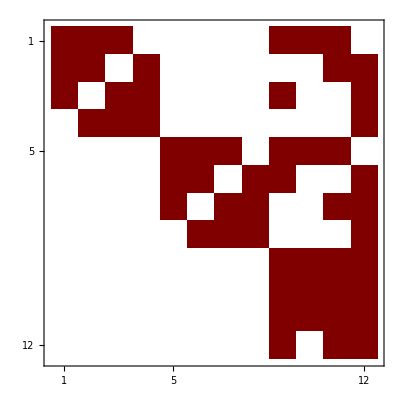

```mathematica
Bmatrix12//MatrixPlot
```

```mathematica
Bmatrix12//MatrixForm
```

(e (Log[1+X1]+Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0
e Log[-1+X2] | e (Log[1+X1]-Log[-1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | e (Log[-1+X1]-Log[1+X1])
-e Log[1+X1] | 0 | e (-Log[1+X1]+Log[-1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X2]+Log[1+X2])
0 | e Log[1+X1] | -e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-1+X2])
0 | 0 | 0 | 0 | e (Log[-1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | -e (Log[1+X1]-Log[-1+X2])+e (-Log[-1+X2]+Log[1+X2]) | -e (Log[1+X1]-Log[-1+X2]) | e (Log[-1+X1]-Log[-1+X2])-e (Log[1+X1]-Log[-1+X2]) | 0
0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (-Log[-1+X1]+Log[1+X1]) | e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | -e (-Log[-1+X1]+Log[1+X1])
0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | -e (Log[-1+X2]-Log[1+X2])
0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | -e (-Log[-1+X1]+Log[1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | -e Log[-2+X1+X2] | e (-Log[-2+X1+X2]+Log[X1+X2]) | e (2 Log[-2+X1+X2]-2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2])

#### level 0

```mathematica
dRep=Thread[(d/@basis12)->Coefficient[Bmatrix12,e].basis12];
```

```mathematica
l0={Log[X1+1],Log[X2+1]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

```mathematica
toPhi=Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{⟨1,3,5,6⟩→φ_1,⟨1,3,5,9⟩→φ_2,⟨1,3,6,7⟩→φ_3,⟨1,3,7,9⟩→φ_4,⟨2,4,5,6⟩→φ_5,⟨2,4,5,9⟩→φ_6,⟨2,4,6,7⟩→φ_7,⟨2,4,7,9⟩→φ_8,⟨3,5,6,7⟩→φ_9,⟨3,5,6,8⟩→φ_10,⟨3,5,6,9⟩→φ_11,⟨3,5,7,9⟩→φ_12,⟨4,5,6,7⟩→φ_13,⟨4,5,6,8⟩→φ_14,⟨4,5,6,9⟩→φ_15,⟨4,5,7,9⟩→φ_16}

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[-1+X1],Log[-1+X2]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨3,5,6,9⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩-⟨3,5,6,8⟩+⟨3,5,6,9⟩}

2

```mathematica
lv2/.toPhi
```

{-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1-φ_2-φ_6-φ_10+φ_11}

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+2 ⟨3,5,6,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-2 ⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩}

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv2Old, i, Basis],{i,1,Length[lv2Old]}]
```

{False,False}

```mathematica
lv2Old/.toPhi
```

{φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11,φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
Basis/.toPhi
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1-φ_2-φ_6-φ_10+φ_11,φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11}

why only the first basis is joined?

```mathematica
lv2[[2]]
```

⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩-⟨3,5,6,8⟩+⟨3,5,6,9⟩

```mathematica
eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lv2Old[[2]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars]
```

{{{c1,c2,c3,c4}[1]→2,{c1,c2,c3,c4}[2]→-1,{c1,c2,c3,c4}[3]→-1,{c1,c2,c3,c4}[4]→-1}}

```mathematica
eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lv2Old[[1]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars]
```

{{{c1,c2,c3,c4}[1]→0,{c1,c2,c3,c4}[2]→0,{c1,c2,c3,c4}[3]→0,{c1,c2,c3,c4}[4]→1}}

```mathematica
eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lv2[[2]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars]
```

{{{c1,c2,c3,c4}[1]→0,{c1,c2,c3,c4}[2]→0,{c1,c2,c3,c4}[3]→1,{c1,c2,c3,c4}[4]→0}}

```mathematica
eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lv2[[1]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars]
```

{{{c1,c2,c3,c4}[1]→0,{c1,c2,c3,c4}[2]→1,{c1,c2,c3,c4}[3]→0,{c1,c2,c3,c4}[4]→0}}

```mathematica
Basis/.toPhi
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1-φ_2-φ_6-φ_10+φ_11,φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3}

here the algorithm is inefficient, since it accept the first and reject the second. But the best way is to add the sum of both.

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩ | 2 ⟨3,5,6,7⟩-2 ⟨3,5,6,9⟩+4 ⟨3,5,7,9⟩
2 ⟨3,5,6,8⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩ | -2 ⟨3,5,6,8⟩-2 ⟨3,5,6,9⟩+4 ⟨3,5,7,9⟩)

{-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩,2 ⟨3,5,6,8⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩}

```mathematica
lv3/.toPhi
```

{-2 φ_9+2 φ_11-4 φ_12,2 φ_10+2 φ_11-4 φ_12}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

5

```mathematica
Basis/.toPhi
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1-φ_2-φ_6-φ_10+φ_11,φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11,-2 φ_9+2 φ_11-4 φ_12}

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

14

```mathematica
lv3Old/.toPhi//MatrixForm
```

(φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11
φ_1-φ_2+φ_3+φ_4-φ_8+2 φ_9+2 φ_12
φ_4-φ_5+φ_6-φ_7-φ_8-2 φ_9-2 φ_12
φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11
φ_2-φ_4+φ_7+φ_8-φ_10-φ_11+2 φ_12
-φ_3-φ_4-φ_6+φ_8+φ_10+φ_11-2 φ_12
-φ_3-φ_5-φ_7+φ_10-φ_11
φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11
φ_1-φ_2+φ_3+φ_4-φ_8+2 φ_9+2 φ_12
-φ_3-φ_4-φ_6+φ_8-φ_10-φ_11+2 φ_12
φ_1-φ_2+φ_3+φ_4-φ_8+2 φ_11-2 φ_12
φ_4-φ_5+φ_6-φ_7-φ_8-2 φ_9-2 φ_12
φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11
φ_2-φ_4+φ_7+φ_8-φ_10-φ_11+2 φ_12)

this is suspicious. Why there is this new 6th basis??

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
lv3Old[[2]]+lv3Old[[3]]/.toPhi
```

φ_1-φ_2+φ_3+2 φ_4-φ_5+φ_6-φ_7-2 φ_8

```mathematica
{lv3Old[[2]]+lv3Old[[3]]};
Table[CheckDependent[%, i, Basis],{i,1,Length[%]}]
```

{False}

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,False,False,True,False,False,True,True,False,False,False,False,True,False}

```mathematica
(*Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]*)
```

```mathematica
Basis=Join[Basis,{lv3Old[[2]]+lv3Old[[3]]}]
```

{⟨1,3,5,6⟩-⟨2,4,5,6⟩,-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨3,5,6,9⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩-⟨3,5,6,8⟩+⟨3,5,6,9⟩,⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+2 ⟨3,5,6,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩,-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+2 ⟨1,3,7,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,6,7⟩-2 ⟨2,4,7,9⟩}

```mathematica
Basis//Length
```

6

```mathematica
Basis/.toPhi
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1-φ_2-φ_6-φ_10+φ_11,φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11,-2 φ_9+2 φ_11-4 φ_12,φ_1-φ_2+φ_3+2 φ_4-φ_5+φ_6-φ_7-2 φ_8}

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

{{}}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,3,2}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

12

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

6

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[-1+X1],Log[1+X1],Log[-1+X2],Log[1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

7

```mathematica
lett=Join[l0,Complement[l1,l0],Complement[l2,l1]]
```

{Log[1+X1],Log[1+X2],Log[-1+X1],Log[-1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

6 = 1 + (2+1) + (1+1)
8 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨3,5,6,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩-⟨3,5,6,8⟩+⟨3,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+2 ⟨3,5,6,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩
-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+2 ⟨1,3,7,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-⟨2,4,6,7⟩-2 ⟨2,4,7,9⟩)

6

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_11
φ_1-φ_2-φ_6-φ_10+φ_11
φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11
-2 φ_9+2 φ_11-4 φ_12
φ_1-φ_2+φ_3+2 φ_4-φ_5+φ_6-φ_7-2 φ_8)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_5

so psi is just the new basis 1.

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basis12[[j]]],{i,1,Length[Basis]},{j,1,Length[basis12]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Bmatrix6=Umatrix.Bmatrix12.Uinv//Simplify;
```

#### check flatness

```mathematica
Bmatrix6//MatrixForm
```

(2 e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[1+X1]-Log[1+X2]) | 0 | 0
1/2 e (Log[-1+X2]+Log[1+X2]-2 Log[-2+X1+X2]) | e Log[-2+X1+X2] | 1/2 e (Log[-1+X2]-Log[1+X2]) | 1/2 e (2 Log[1+X1]-Log[-1+X2]-Log[1+X2]+2 Log[-2+X1+X2]) | 1/2 e (-Log[-1+X2]+Log[1+X2]+2 Log[-2+X1+X2]-2 Log[X1+X2]) | 1/2 e (-Log[-1+X2]+Log[1+X2])
-1/2 e (Log[-1+X1]+Log[1+X1]-2 (2 Log[1+X2]+Log[-2+X1+X2])) | e (Log[-1+X1]-Log[1+X2]-Log[-2+X1+X2]) | 1/2 e (Log[-1+X1]+Log[1+X1]-2 Log[1+X2]) | 1/2 e (Log[-1+X1]+Log[1+X1]-2 (Log[1+X2]+Log[-2+X1+X2])) | 1/2 e (Log[-1+X1]-Log[1+X1]-2 Log[-2+X1+X2]+2 Log[X1+X2]) | 1/2 e (-Log[-1+X1]+Log[1+X1])
-1/2 e (Log[-1+X2]-3 Log[1+X2]+2 Log[2+X1+X2]) | e (Log[-1+X1]-Log[1+X2]+Log[2+X1+X2]) | 1/2 e (Log[-1+X2]-Log[1+X2]) | 1/2 e (Log[-1+X2]-Log[1+X2]+2 Log[2+X1+X2]) | 1/2 e (Log[-1+X2]-Log[1+X2]-2 Log[X1+X2]+2 Log[2+X1+X2]) | 1/2 e (Log[-1+X2]-Log[1+X2])
e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]) | 0 | -e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]) | 0
1/2 e (-Log[-1+X1]+Log[1+X1]+Log[-1+X2]+3 Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]) | 1/2 e (Log[-1+X1]-Log[1+X1]+Log[-1+X2]-Log[1+X2]) | 1/2 e (Log[-1+X1]+Log[1+X1]-Log[-1+X2]-Log[1+X2]) | 1/2 e (Log[-1+X1]+Log[1+X1]-Log[-1+X2]-Log[1+X2]) | -1/2 e (Log[-1+X1]+Log[1+X1]+Log[-1+X2]+Log[1+X2]))

```mathematica
Bmatrix6;
Table[D[%,kin[[i]]].D[%,kin[[j]]]-D[%,kin[[j]]].D[%,kin[[i]]]//Simplify,{i,1,Length[kin]},{j,i+1,Length[kin]}]//Flatten//DeleteCases[0]
```

{}

```mathematica
lett
```

{Log[1+X1],Log[1+X2],Log[-1+X1],Log[-1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

```mathematica
{Log[1+X1],Log[1+X2],Log[-1+X1],Log[-1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}/.{X1->Subscript[X, 1],X2->Subscript[X, 2]}
```

{Log[1+X_1],Log[1+X_2],Log[-1+X_1],Log[-1+X_2],Log[-2+X_1+X_2],Log[X_1+X_2],Log[2+X_1+X_2]}

```mathematica
B6=Coefficient[Bmatrix6,e]/. Thread[lett->Table[ToExpression["L"<>ToString[i]],{i,1,Length[lett]}]]//Simplify;
%//MatrixForm
```

(2 L2 | -L2+L3 | -L2+L4 | L1-L2 | 0 | 0
1/2 (L2+L4-2 L5) | L5 | 1/2 (-L2+L4) | L1-L2/2-L4/2+L5 | 1/2 (L2-L4+2 L5-2 L6) | (L2-L4)/2
-L1/2+2 L2-L3/2+L5 | -L2+L3-L5 | 1/2 (L1-2 L2+L3) | 1/2 (L1+L3-2 (L2+L5)) | 1/2 (-L1+L3-2 L5+2 L6) | (L1-L3)/2
1/2 (3 L2-L4-2 L7) | -L2+L3+L7 | 1/2 (-L2+L4) | 1/2 (-L2+L4+2 L7) | 1/2 (-L2+L4-2 L6+2 L7) | 1/2 (-L2+L4)
L5+L7 | -L5-L7 | 0 | -L5-L7 | -L5-L7 | 0
1/2 (L1+3 L2-L3+L4) | -L2+L3 | 1/2 (-L1-L2+L3+L4) | 1/2 (L1-L2+L3-L4) | 1/2 (L1-L2+L3-L4) | 1/2 (-L1-L2-L3-L4))

```mathematica
B6/.{L1->Subscript[L, 1],L2->Subscript[L, 2],L3->Subscript[L, 3],L4->Subscript[L, 4],L5->Subscript[L, 5],L6->Subscript[L, 6],L7->Subscript[L, 7]}//MatrixForm
```

(2 L_2 | -L_2+L_3 | -L_2+L_4 | L_1-L_2 | 0 | 0
1/2 (L_2+L_4-2 L_5) | L_5 | 1/2 (-L_2+L_4) | L_1-L_2/2-L_4/2+L_5 | 1/2 (L_2-L_4+2 L_5-2 L_6) | 1/2 (L_2-L_4)
-L_1/2+2 L_2-L_3/2+L_5 | -L_2+L_3-L_5 | 1/2 (L_1-2 L_2+L_3) | 1/2 (L_1+L_3-2 (L_2+L_5)) | 1/2 (-L_1+L_3-2 L_5+2 L_6) | 1/2 (L_1-L_3)
1/2 (3 L_2-L_4-2 L_7) | -L_2+L_3+L_7 | 1/2 (-L_2+L_4) | 1/2 (-L_2+L_4+2 L_7) | 1/2 (-L_2+L_4-2 L_6+2 L_7) | 1/2 (-L_2+L_4)
L_5+L_7 | -L_5-L_7 | 0 | -L_5-L_7 | -L_5-L_7 | 0
1/2 (L_1+3 L_2-L_3+L_4) | -L_2+L_3 | 1/2 (-L_1-L_2+L_3+L_4) | 1/2 (L_1-L_2+L_3-L_4) | 1/2 (L_1-L_2+L_3-L_4) | 1/2 (-L_1-L_2-L_3-L_4))

```mathematica
vec={ψ,F1,F1t,F2,G,H};
list={L1,L2,L3,L4,L5,L6,L7};
Table[Coefficient[B6[[1]].vec,list[[i]]],{i,1,7}]
Table[Coefficient[B6[[2]].vec,list[[i]]],{i,1,7}]
Table[Coefficient[B6[[3]].vec,list[[i]]],{i,1,7}]
Table[Coefficient[B6[[4]].vec,list[[i]]],{i,1,7}]
Table[Coefficient[B6[[5]].vec,list[[i]]],{i,1,7}]
Table[Coefficient[B6[[6]].vec,list[[i]]],{i,1,7}]
```

{F2,-F1-F1t-F2+2 ψ,F1,F1t,0,0,0}

{F2,-F1t/2-F2/2+G/2+H/2+ψ/2,0,F1t/2-F2/2-G/2-H/2+ψ/2,F1+F2+G-ψ,-G,0}

{F1t/2+F2/2-G/2+H/2-ψ/2,-F1-F1t-F2+2 ψ,F1+F1t/2+F2/2+G/2-H/2-ψ/2,0,-F1-F2-G+ψ,G,0}

{0,-F1-F1t/2-F2/2-G/2-H/2+(3 ψ)/2,F1,F1t/2+F2/2+G/2+H/2-ψ/2,0,-G,F1+F2+G-ψ}

{0,0,0,0,-F1-F2-G+ψ,0,-F1-F2-G+ψ}

{-F1t/2+F2/2+G/2-H/2+ψ/2,-F1-F1t/2-F2/2-G/2-H/2+(3 ψ)/2,F1+F1t/2+F2/2+G/2-H/2-ψ/2,F1t/2-F2/2-G/2-H/2+ψ/2,0,0,0}

```mathematica
Table[Coefficient[(2*B6[[1]]-B6[[2]]-B6[[3]]-B6[[4]]).vec,list[[i]]],{i,1,7}]
```

{-F1t/2+F2/2+G/2-H/2+ψ/2,0,-F1t/2-F2/2-G/2+H/2+ψ/2,F1t,0,G,-F1-F2-G+ψ}

```mathematica
B6/.{L2->0,L4->0}//MatrixForm
```

(0 | L3 | 0 | L1 | 0 | 0
-L5 | L5 | 0 | L1+L5 | 1/2 (2 L5-2 L6) | 0
-L1/2-L3/2+L5 | L3-L5 | (L1+L3)/2 | 1/2 (L1+L3-2 L5) | 1/2 (-L1+L3-2 L5+2 L6) | (L1-L3)/2
-L7 | L3+L7 | 0 | L7 | 1/2 (-2 L6+2 L7) | 0
L5+L7 | -L5-L7 | 0 | -L5-L7 | -L5-L7 | 0
(L1-L3)/2 | L3 | 1/2 (-L1+L3) | (L1+L3)/2 | (L1+L3)/2 | 1/2 (-L1-L3))

```mathematica
B6/.{L1->0,L3->0}//MatrixForm
```

(2 L2 | -L2 | -L2+L4 | -L2 | 0 | 0
1/2 (L2+L4-2 L5) | L5 | 1/2 (-L2+L4) | -L2/2-L4/2+L5 | 1/2 (L2-L4+2 L5-2 L6) | (L2-L4)/2
2 L2+L5 | -L2-L5 | -L2 | -L2-L5 | 1/2 (-2 L5+2 L6) | 0
1/2 (3 L2-L4-2 L7) | -L2+L7 | 1/2 (-L2+L4) | 1/2 (-L2+L4+2 L7) | 1/2 (-L2+L4-2 L6+2 L7) | 1/2 (-L2+L4)
L5+L7 | -L5-L7 | 0 | -L5-L7 | -L5-L7 | 0
1/2 (3 L2+L4) | -L2 | 1/2 (-L2+L4) | 1/2 (-L2-L4) | 1/2 (-L2-L4) | 1/2 (-L2-L4))

```mathematica
Basis/.toPhi
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1-φ_2-φ_6-φ_10+φ_11,φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11,-2 φ_9+2 φ_11-4 φ_12,φ_1-φ_2+φ_3+2 φ_4-φ_5+φ_6-φ_7-2 φ_8}

### filter: X1 only

```mathematica
Bmatrix12//MatrixForm
```

(e (Log[1+X1]+Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0
e Log[-1+X2] | e (Log[1+X1]-Log[-1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | e (Log[-1+X1]-Log[1+X1])
-e Log[1+X1] | 0 | e (-Log[1+X1]+Log[-1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X2]+Log[1+X2])
0 | e Log[1+X1] | -e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-1+X2])
0 | 0 | 0 | 0 | e (Log[-1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | -e (Log[1+X1]-Log[-1+X2])+e (-Log[-1+X2]+Log[1+X2]) | -e (Log[1+X1]-Log[-1+X2]) | e (Log[-1+X1]-Log[-1+X2])-e (Log[1+X1]-Log[-1+X2]) | 0
0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (-Log[-1+X1]+Log[1+X1]) | e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | -e (-Log[-1+X1]+Log[1+X1])
0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | -e (Log[-1+X2]-Log[1+X2])
0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | -e (-Log[-1+X1]+Log[1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | -e Log[-2+X1+X2] | e (-Log[-2+X1+X2]+Log[X1+X2]) | e (2 Log[-2+X1+X2]-2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2])

```mathematica
Bmatrix12x1=Bmatrix12/.{Log[-1+X2]->0,Log[1+X2]->0};
%//MatrixForm
```

(e Log[1+X1] | 0 | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | e Log[1+X1] | e Log[-1+X1] | 0 | 0
0 | e Log[1+X1] | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[-1+X1] | e (Log[-1+X1]-Log[1+X1])
-e Log[1+X1] | 0 | -e Log[1+X1] | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1] | 0 | 0 | 0
0 | e Log[1+X1] | 0 | -e Log[1+X1] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X1]
0 | 0 | 0 | 0 | e Log[-1+X1] | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | -e Log[1+X1] | -e Log[1+X1] | e Log[-1+X1]-e Log[1+X1] | 0
0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | 0 | e (-Log[-1+X1]+Log[1+X1]) | -e Log[1+X1] | 0 | 0 | -e (-Log[-1+X1]+Log[1+X1])
0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | -e Log[-1+X1] | 0 | 0 | 0 | -e Log[-1+X1] | 0
0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | 0 | -e Log[-1+X1] | 0 | 0 | 0 | e Log[-1+X1]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | -e Log[-2+X1+X2] | e (-Log[-2+X1+X2]+Log[X1+X2]) | e (2 Log[-2+X1+X2]-2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2])

#### level 0

```mathematica
dRep=Thread[(d/@basis12)->Coefficient[Bmatrix12x1,e].basis12];
```

```mathematica
l0={Log[X1+1],Log[X2+1]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

```mathematica
toPhi=Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{⟨1,3,5,6⟩→φ_1,⟨1,3,5,9⟩→φ_2,⟨1,3,6,7⟩→φ_3,⟨1,3,7,9⟩→φ_4,⟨2,4,5,6⟩→φ_5,⟨2,4,5,9⟩→φ_6,⟨2,4,6,7⟩→φ_7,⟨2,4,7,9⟩→φ_8,⟨3,5,6,7⟩→φ_9,⟨3,5,6,8⟩→φ_10,⟨3,5,6,9⟩→φ_11,⟨3,5,7,9⟩→φ_12,⟨4,5,6,7⟩→φ_13,⟨4,5,6,8⟩→φ_14,⟨4,5,6,9⟩→φ_15,⟨4,5,7,9⟩→φ_16}

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[-1+X1]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨3,5,6,9⟩}

1

```mathematica
lv2/.toPhi
```

{-φ_3-φ_5-φ_7+φ_10-φ_11}

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+2 ⟨3,5,6,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩,0}

```mathematica
lv2Old/.toPhi
```

{φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11,0}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

3

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,2}

here the algorithm is inefficient, since it accept the first and reject the second. But the best way is to add the sum of both.

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩ | 2 ⟨3,5,6,7⟩-2 ⟨3,5,6,9⟩+4 ⟨3,5,7,9⟩
2 ⟨3,5,6,8⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩ | -2 ⟨3,5,6,8⟩-2 ⟨3,5,6,9⟩+4 ⟨3,5,7,9⟩)

{-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩,2 ⟨3,5,6,8⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩}

```mathematica
lv3/.toPhi
```

{-2 φ_9+2 φ_11-4 φ_12,2 φ_10+2 φ_11-4 φ_12}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

4

```mathematica
Basis/.toPhi
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11,-2 φ_9+2 φ_11-4 φ_12}

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

3

```mathematica
lv3Old/.toPhi
```

{φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11,-φ_3-φ_5-φ_7+φ_10-φ_11,φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11}

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,True,True}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

Part::partw: Part {6} of {⟨1,3,5,6⟩-⟨2,4,5,6⟩,-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨3,5,6,9⟩,⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+2 ⟨3,5,6,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩,-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩} does not exist.

{}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,2,1}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

2

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

4

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[-1+X1],Log[1+X1],Log[1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

6

6 = 1 + (2+1) + (1+1)
8 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
-⟨1,3,6,7⟩-⟨2,4,5,6⟩-⟨2,4,6,7⟩+⟨3,5,6,8⟩-⟨3,5,6,9⟩
⟨1,3,5,6⟩+⟨1,3,6,7⟩+⟨2,4,6,7⟩+2 ⟨3,5,6,7⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩
-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩)

4

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_11
φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11
-2 φ_9+2 φ_11-4 φ_12)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_5

so psi is just the new basis 1.

#### A matrix (associated to physical basis): impose symmetry

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basis12[[j]]],{i,1,Length[Basis]},{j,1,Length[basis12]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Bmatrix6x1=Umatrix.Bmatrix12x1.Uinv//Simplify;
%//MatrixForm
```

(0 | e Log[-1+X1] | e Log[1+X1] | 0
-e Log[-2+X1+X2] | e Log[-2+X1+X2] | e (Log[1+X1]+Log[-2+X1+X2]) | e (Log[-2+X1+X2]-Log[X1+X2])
-e Log[2+X1+X2] | e (Log[-1+X1]+Log[2+X1+X2]) | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2])
e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]))

{1,2,3} {4,5} {6,7,8}
notice that l7, l8 are suspicious poles. To eliminate the spurious poles, we may further reduce the size. (there is further redundancy in the integral repr. of Hankel function)
6 = 1 + (2+1) + (1+1)

```mathematica
(*lett=Join[l0,Complement[l1,l0],Complement[l2,l1]]*)
```

the matrix is not upper triangular...

```mathematica
B6x1=Coefficient[Bmatrix6x1,e]/. Thread[lett->Table[ToExpression["L"<>ToString[i]],{i,1,Length[lett]}]]//Simplify
```

{{0,L3,L1,0},{-L5,L5,L1+L5,L5-L6},{-L7,L3+L7,L7,-L6+L7},{L5+L7,-L5-L7,-L5-L7,-L5-L7}}

```mathematica
%//MatrixForm
```

(0 | L3 | L1 | 0
-L5 | L5 | L1+L5 | L5-L6
-L7 | L3+L7 | L7 | -L6+L7
L5+L7 | -L5-L7 | -L5-L7 | -L5-L7)

```mathematica
({{0, L3, L1, 0}, {-L5, L5, L1+L5, L5-L6}, {-L7, L3+L7, L7, -L6+L7}, {L5+L7, -L5-L7, -L5-L7, -L5-L7}})/.{L1->Subscript[L, 1],L2->Subscript[L, 2],L3->Subscript[L, 3],L4->Subscript[L, 4],L5->Subscript[L, 5],L6->Subscript[L, 6],L7->Subscript[L, 7]}//MatrixForm
```

(0 | L_3 | L_1 | 0
-L_5 | L_5 | L_1+L_5 | L_5-L_6
-L_7 | L_3+L_7 | L_7 | -L_6+L_7
L_5+L_7 | -L_5-L_7 | -L_5-L_7 | -L_5-L_7)

#### Do we need to do the filtering again? Since it is obvious that we only need 5 basis.

### filter: X2 only

```mathematica
Bmatrix12//MatrixForm
```

(e (Log[1+X1]+Log[-1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | e (-Log[-1+X1]+Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | e (Log[1+X1]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0
e Log[-1+X2] | e (Log[1+X1]-Log[-1+X2]) | 0 | e (Log[-1+X1]-Log[1+X1]) | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | e (Log[-1+X1]-Log[1+X1])
-e Log[1+X1] | 0 | e (-Log[1+X1]+Log[-1+X2]) | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X2]+Log[1+X2])
0 | e Log[1+X1] | -e Log[-1+X2] | e (-Log[1+X1]-Log[-1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e (-Log[1+X1]+Log[-1+X2])
0 | 0 | 0 | 0 | e (Log[-1+X1]+Log[1+X2]) | e (Log[-1+X2]-Log[1+X2]) | e (Log[-1+X1]-Log[1+X1]) | 0 | -e (Log[1+X1]-Log[-1+X2])+e (-Log[-1+X2]+Log[1+X2]) | -e (Log[1+X1]-Log[-1+X2]) | e (Log[-1+X1]-Log[-1+X2])-e (Log[1+X1]-Log[-1+X2]) | 0
0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[-1+X1]-Log[1+X2]) | 0 | e (-Log[-1+X1]+Log[1+X1]) | e (-Log[1+X1]+Log[1+X2]) | 0 | 0 | -e (-Log[-1+X1]+Log[1+X1])
0 | 0 | 0 | 0 | -e Log[-1+X1] | 0 | e (-Log[-1+X1]+Log[1+X2]) | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | e (-Log[-1+X1]+Log[-1+X2]) | -e (Log[-1+X2]-Log[1+X2])
0 | 0 | 0 | 0 | 0 | e Log[-1+X1] | -e Log[1+X2] | e (-Log[-1+X1]-Log[1+X2]) | 0 | 0 | 0 | -e (-Log[-1+X1]+Log[1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | -e Log[-2+X1+X2] | e (-Log[-2+X1+X2]+Log[X1+X2]) | e (2 Log[-2+X1+X2]-2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2])

```mathematica
Bmatrix12x2=Bmatrix12/.{Log[-1+X1]->0,Log[1+X1]->0};
%//MatrixForm
```

(e Log[-1+X2] | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X2] | -e Log[1+X2] | e (Log[-1+X2]-Log[1+X2]) | 0
e Log[-1+X2] | -e Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X2] | 0
0 | 0 | e Log[-1+X2] | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | 0 | 0 | e Log[1+X2] | 0 | 0 | e (-Log[-1+X2]+Log[1+X2])
0 | 0 | -e Log[-1+X2] | -e Log[-1+X2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[-1+X2]
0 | 0 | 0 | 0 | e Log[1+X2] | e (Log[-1+X2]-Log[1+X2]) | 0 | 0 | e Log[-1+X2]+e (-Log[-1+X2]+Log[1+X2]) | e Log[-1+X2] | 0 | 0
0 | 0 | 0 | 0 | e Log[1+X2] | -e Log[1+X2] | 0 | 0 | e Log[1+X2] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | e Log[1+X2] | e (-Log[-1+X2]+Log[1+X2]) | 0 | 0 | e Log[-1+X2] | -e (Log[-1+X2]-Log[1+X2])
0 | 0 | 0 | 0 | 0 | 0 | -e Log[1+X2] | -e Log[1+X2] | 0 | 0 | 0 | -e Log[1+X2]
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[2+X1+X2] | e (-Log[X1+X2]+Log[2+X1+X2]) | e (2 Log[X1+X2]-2 Log[2+X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | e Log[X1+X2] | e Log[-2+X1+X2] | e (Log[-2+X1+X2]-Log[X1+X2]) | e (-2 Log[-2+X1+X2]+2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | -e Log[-2+X1+X2] | e (-Log[-2+X1+X2]+Log[X1+X2]) | e (2 Log[-2+X1+X2]-2 Log[X1+X2])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -e Log[X1+X2] | 0 | e Log[X1+X2] | -2 e Log[X1+X2])

#### level 0

```mathematica
dRep=Thread[(d/@basis12)->Coefficient[Bmatrix12x2,e].basis12];
```

```mathematica
l0={Log[X1+1],Log[X2+1]};(*old letters*)
```

```mathematica
Basis={psi};
```

```mathematica
BasisCount={1};
```

```mathematica
toPhi=Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{⟨1,3,5,6⟩→φ_1,⟨1,3,5,9⟩→φ_2,⟨1,3,6,7⟩→φ_3,⟨1,3,7,9⟩→φ_4,⟨2,4,5,6⟩→φ_5,⟨2,4,5,9⟩→φ_6,⟨2,4,6,7⟩→φ_7,⟨2,4,7,9⟩→φ_8,⟨3,5,6,7⟩→φ_9,⟨3,5,6,8⟩→φ_10,⟨3,5,6,9⟩→φ_11,⟨3,5,7,9⟩→φ_12,⟨4,5,6,7⟩→φ_13,⟨4,5,6,8⟩→φ_14,⟨4,5,6,9⟩→φ_15,⟨4,5,7,9⟩→φ_16}

#### level 1

all letters appeared until level 1:

```mathematica
d1=psi/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l1=Cases[%,_Log,Infinity]//Union;
Complement[l1,l0]
```

{Log[-1+X2]}

only add the basis for new letters:

```mathematica
lv2=Coefficient[d1,#]&/@Complement[l1,l0]
%//Length
```

{⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩-⟨3,5,6,8⟩+⟨3,5,6,9⟩}

1

```mathematica
lv2/.toPhi
```

{φ_1-φ_2-φ_6-φ_10+φ_11}

```mathematica
Basis=Join[Basis,lv2];
```

then add the basis for old letters if linearly-independent:

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
sol=Solve[eqn==0,Cases[eqn,_c,Infinity]//Union](*//First*);
Return[If[sol=!={},True,False]]]
```

```mathematica
lv2Old=Coefficient[d1,#]&/@l0//Flatten
```

{0,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-2 ⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩}

```mathematica
lv2Old/.toPhi
```

{0,φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11}

```mathematica
Do[If[!CheckDependent[lv2Old,i,Basis],Basis=Join[Basis,{lv2Old[[i]]}];],{i,Length[lv2Old]}]
```

```mathematica
Basis//Length
```

3

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,2}

here the algorithm is inefficient, since it accept the first and reject the second. But the best way is to add the sum of both.

#### level 2

```mathematica
d2=Basis[[(BasisCount[[;;-2]]//Total)+1;;]]/.AngleBracket[a___]->d[AngleBracket[a]]/.dRep;
l2=Cases[%,_Log,Infinity]//Union;
Complement[l2,l1]
```

{Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

```mathematica
Coefficient[d2,#]&/@Complement[l2,l1];(*new letters*)
(Sort[{#,-#}]&/@Flatten[%])//Union ;(*this seems to be a key step: from 5x4 to 4*)
%//MatrixForm
lv3=%[[All;;,1]]//DeleteCases[0]
```

(0 | 0
-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩ | 2 ⟨3,5,6,7⟩-2 ⟨3,5,6,9⟩+4 ⟨3,5,7,9⟩
2 ⟨3,5,6,8⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩ | -2 ⟨3,5,6,8⟩-2 ⟨3,5,6,9⟩+4 ⟨3,5,7,9⟩)

{-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩,2 ⟨3,5,6,8⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩}

```mathematica
lv3/.toPhi
```

{-2 φ_9+2 φ_11-4 φ_12,2 φ_10+2 φ_11-4 φ_12}

```mathematica
Do[If[! CheckDependent[lv3, i, Basis], Basis = Join[Basis, {lv3[[i]]}];], {i, Length[lv3]}];
Basis//Length
```

4

```mathematica
Basis/.toPhi
```

{φ_1-φ_5,φ_1-φ_2-φ_6-φ_10+φ_11,φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11,-2 φ_9+2 φ_11-4 φ_12}

```mathematica
lv3Old = Coefficient[d2, #] & /@Join[ l0,l1] // Flatten//DeleteCases[0];
```

```mathematica
lv3Old//Length
```

3

```mathematica
lv3Old/.toPhi
```

{φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11,φ_1-φ_2-φ_6-φ_10+φ_11,φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11}

```mathematica
CheckDependent[lvn_List,i_,Basis_List]:=Module[{eqn,vars,sol},eqn=Coefficient[Basis.(c/@Range[Length[Basis]])-lvn[[i]],#]&/@basisNeed;
vars=Union@Cases[eqn,_c,Infinity];
sol=Quiet@Solve[Thread[eqn==0],vars];
sol=!={}]
```

```mathematica
Table[CheckDependent[lv3Old, i, Basis],{i,1,Length[lv3Old]}]
```

{True,True,True}

```mathematica
Do[If[! CheckDependent[lv3Old, i, Basis], Basis = Join[Basis, {lv3Old[[i]]}];], {i, Length[lv3Old]}]
```

```mathematica
Basis//Length
```

4

```mathematica
Position[lv3Old,#]&/@Basis[[{6}]]
```

Part::partw: Part {6} of {⟨1,3,5,6⟩-⟨2,4,5,6⟩,⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩-⟨3,5,6,8⟩+⟨3,5,6,9⟩,⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-2 ⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩,-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩} does not exist.

{}

```mathematica
AppendTo[BasisCount,Length[Basis]-Total[BasisCount]]
```

{1,2,1}

#### close at level 3

```mathematica
d3 = Basis[[(BasisCount[[;; -2]] // Total) + 1 ;;]] /. AngleBracket[a___] -> d[AngleBracket[a]] /. dRep;
l3 = Cases[%, _Log, Infinity] // Union;
Complement[l3, l2]
```

{}

```mathematica
lv4Old = Coefficient[d3, #] & /@ Join[ l0, l1, l2] // Flatten // DeleteCases[0];
```

```mathematica
lv4Old // Length
```

2

```mathematica
Do[If[! CheckDependent[lv4Old, i, Basis], Basis = Join[Basis, {lv4Old[[i]]}];], {i, Length[lv4Old]}]
```

```mathematica
Basis // Length
```

4

#### summary: all physical basis

```mathematica
letters={l0,l1,l2}//Flatten//Union
%//Length
```

{Log[1+X1],Log[-1+X2],Log[1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

6

6 = 1 + (2+1) + (1+1)
8 = 3 + 2 + 3

```mathematica
Basis//MatrixForm
Basis//Length
```

(⟨1,3,5,6⟩-⟨2,4,5,6⟩
⟨1,3,5,6⟩-⟨1,3,5,9⟩-⟨2,4,5,9⟩-⟨3,5,6,8⟩+⟨3,5,6,9⟩
⟨1,3,5,9⟩-⟨2,4,5,6⟩+⟨2,4,5,9⟩-2 ⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩
-2 ⟨3,5,6,7⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩)

4

see how this 6d subspace is embedded in the previous 50d space:

```mathematica
BasisIndex=Basis/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])];
%//MatrixForm
```

(φ_1-φ_5
φ_1-φ_2-φ_6-φ_10+φ_11
φ_2-φ_5+φ_6-2 φ_9-φ_10-φ_11
-2 φ_9+2 φ_11-4 φ_12)

```mathematica
psi/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_1-φ_5

so psi is just the new basis 1.

#### A matrix (associated to physical basis): impose symmetry

```mathematica
Umatrix=Table[Coefficient[Basis[[i]],basis12[[j]]],{i,1,Length[Basis]},{j,1,Length[basis12]}];
Uinv=Simplify[PseudoInverse[Umatrix]];
```

```mathematica
Bmatrix6x2=Umatrix.Bmatrix12x2.Uinv//Simplify;
%//MatrixForm
```

(0 | e Log[-1+X2] | e Log[1+X2] | 0
-e Log[-2+X1+X2] | e Log[-2+X1+X2] | e (Log[1+X2]+Log[-2+X1+X2]) | e (-Log[-2+X1+X2]+Log[X1+X2])
-e Log[2+X1+X2] | e (Log[-1+X2]+Log[2+X1+X2]) | e Log[2+X1+X2] | e (Log[X1+X2]-Log[2+X1+X2])
-e (Log[-2+X1+X2]+Log[2+X1+X2]) | e (Log[-2+X1+X2]+Log[2+X1+X2]) | e (Log[-2+X1+X2]+Log[2+X1+X2]) | -e (Log[-2+X1+X2]+Log[2+X1+X2]))

{1,2,3} {4,5} {6,7,8}
notice that l7, l8 are suspicious poles. To eliminate the spurious poles, we may further reduce the size. (there is further redundancy in the integral repr. of Hankel function)
6 = 1 + (2+1) + (1+1)

```mathematica
(*lett=Join[l0,Complement[l1,l0],Complement[l2,l1]]*)
```

```mathematica
lett
```

{Log[1+X1],Log[1+X2],Log[-1+X1],Log[-1+X2],Log[-2+X1+X2],Log[X1+X2],Log[2+X1+X2]}

the matrix is not upper triangular...

```mathematica
B6x2=Coefficient[Bmatrix6x2,e]/. Thread[lett->Table[ToExpression["L"<>ToString[i]],{i,1,Length[lett]}]]//Simplify
```

{{0,L4,L2,0},{-L5,L5,L2+L5,-L5+L6},{-L7,L4+L7,L7,L6-L7},{-L5-L7,L5+L7,L5+L7,-L5-L7}}

```mathematica
%//MatrixForm
```

(0 | L4 | L2 | 0
-L5 | L5 | L2+L5 | -L5+L6
-L7 | L4+L7 | L7 | L6-L7
-L5-L7 | L5+L7 | L5+L7 | -L5-L7)

```mathematica
({{0, L4, L2, 0}, {-L5, L5, L2+L5, -L5+L6}, {-L7, L4+L7, L7, L6-L7}, {-L5-L7, L5+L7, L5+L7, -L5-L7}})/.{L1->Subscript[L, 1],L2->Subscript[L, 2],L3->Subscript[L, 3],L4->Subscript[L, 4],L5->Subscript[L, 5],L6->Subscript[L, 6],L7->Subscript[L, 7]}//MatrixForm
```

(0 | L_4 | L_2 | 0
-L_5 | L_5 | L_2+L_5 | -L_5+L_6
-L_7 | L_4+L_7 | L_7 | L_6-L_7
-L_5-L_7 | L_5+L_7 | L_5+L_7 | -L_5-L_7)

```mathematica
-B6x2[[1]]+B6x2[[2]]+B6x2[[3]]-B6x2[[4]]
```

{0,0,0,2 L6}

we can further do the linear transformation.

```mathematica
U={{1,0,0,0},{-1,1,1,-1},{0,1,0,0},{0,0,1,0}};
%//Det
```

-1

```mathematica
U.B6x2.Inverse[U]//MatrixForm
```

(0 | 0 | L4 | L2
-2 L6 | -2 L6 | 2 L6 | 2 L6
-L6 | L5-L6 | L6 | L2+L6
-L6 | -L6+L7 | L4+L6 | L6)

```mathematica
V={{1,0,0,0},{0,0,1,0},{0,0,0,1},{1,1,-1,-1}};
%//Det
```

1

```mathematica
V.U.B6x2.Inverse[U].Inverse[V]//MatrixForm
```

(0 | L4 | L2 | 0
-L5 | L5 | L2+L5 | L5-L6
-L7 | L4+L7 | L7 | -L6+L7
L5+L7 | -L5-L7 | -L5-L7 | -L5-L7)

## On symmetry conditions

### Impose symmetry from integral

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨3,5,6,7⟩->⟨4,5,6,9⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨4,5,6,9⟩}/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{φ_16→-φ_12,φ_9→φ_15,φ_13→φ_11,φ_14→-φ_10-φ_11-φ_15}

```mathematica
BasisIndex
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_13,φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15,φ_1+φ_3+φ_7+φ_9-φ_14,φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16,φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16}

```mathematica
BasisIndex//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_13
φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15
φ_1+φ_3+φ_7+φ_9-φ_14
φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16
φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16)

```mathematica
BasisSym=BasisIndex/.symForBasis;
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_11
φ_1-φ_2-φ_6-φ_10+φ_11
φ_1+φ_3+φ_7+φ_10+φ_11+2 φ_15
-2 φ_11+4 φ_12+2 φ_15
φ_1-φ_2+φ_3+φ_4-φ_8+2 φ_12+2 φ_15)

```mathematica
lett
```

{Log[X1+Y],Log[X2+Y],Log[Y],Log[X1-Y],Log[X2-Y],Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Table[Coefficient[BasisSym[[i]],Subscript[φ,j]],{i,1,6},{j,1,16}];
%//MatrixRank
```

6

```mathematica
A6//MatrixForm
```

(2 (L2-2 L3) | -L2+L4 | -L2+L5 | L1-L2 | 0 | 0
L2-L7 | -3 L3+L7 | -L2+L5 | L1-L2-L3+L7 | -L2+L5+L6-L7 | L2-L5
2 L2-2 L3-L4+L7 | -L2+L3+L4-L7 | -L2-2 L3+L4 | -L2+L3+L4-L7 | -L6+L7 | L1-L4
L2-L8 | -L2-L3+L4+L8 | 0 | -3 L3+L8 | L2-L5+L6-L8 | -L2+L5
2 L3-L7-L8 | -2 L3+L7+L8 | 0 | -2 L3+L7+L8 | -L7-L8 | 0
L2+L3-L4-L8 | -L2-L3+L4+L8 | -L3+L4 | -2 L3+L4+L8 | L2-L8 | -L2-L4)

```mathematica
{{1,1,0},{1,0,1},{a,b,c}}//Det
```

a-b-c

```mathematica
{{1,0,0,0},{-1,1,1,0},{-1,1,0,1},{2,-1,-1,-1}}//Det
```

1

```mathematica
{{1,0,0,0},{-1,1,1,0},{-1,1,0,1},{2,-1,-1,-1}}//Inverse
```

{{1,0,0,0},{0,1,1,1},{1,0,-1,-1},{1,-1,0,-1}}

```mathematica
BasisIndex[[{2,3,4}]]//Total
```

2 φ_1-φ_2-φ_5-φ_6+φ_9+φ_10+φ_11+φ_15

#### Basis transformation

```mathematica
U={{1,0,0,0,0,0},{-1,1,1,0,0,0},{-1,1,0,1,0,0},{2,-1,-1,-1,0,0},
{1,0,-1,-1,0,1},{-1,1,0,1,-1,0}};
%//Det
```

1

```mathematica
Uinv={{1,0,0,0,0,0},{-1,1,1,0,0,0},{-1,1,0,1,0,0},{2,-1,-1,-1,0,0},
{1,0,-1,-1,0,1},{-1,1,0,1,-1,0}}//Inverse
```

{{1,0,0,0,0,0},{0,1,1,1,0,0},{1,0,-1,-1,0,0},{1,-1,0,-1,0,0},{0,0,1,0,0,-1},{1,-1,-1,-2,1,0}}

```mathematica
U.Table[Subscript[a, i],{i,1,6}]
```

{a_1,-a_1+a_2+a_3,-a_1+a_2+a_4,2 a_1-a_2-a_3-a_4,a_1-a_3-a_4+a_6,-a_1+a_2+a_4-a_5}

```mathematica
B6=U.A6.Uinv//Simplify;
%//MatrixForm
```

(L1-4 L3+L5 | -L1+L4 | L4-L5 | -L1+L2+L4-L5 | 0 | 0
L1-L5 | -L1-2 L3+L5 | -L1-L2+2 L5 | -2 L1+2 L5 | L1+L2-L4-L5 | L2-L5
0 | 0 | -4 L3+2 L6 | 0 | 0 | -2 L6+L7+L8
-L3+L5 | 0 | L1+L3-L5-L6 | L1-2 L3-L5 | -L1+L4 | L6-L8
0 | -L3+L5 | L1-2 L3+L5 | L1-2 L3+L5 | -L1-L5 | -L5+L7
0 | 0 | -2 L3+2 L6 | 0 | 0 | -2 L6)

indeed, L7 and L8 only appear for J6.

#### dJ_2

```mathematica
-A6[[1]]+A6[[2]]+A6[[3]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{L2+2 L3-L4,-2 L3,-L2-2 L3+L4,-L2+L4,-L2+L5,L1+L2-L4-L5}

(L2+2 L3-L4) x_1-2 L3 x_2+(-L2-2 L3+L4) x_3+(-L2+L4) x_4+(-L2+L5) x_5+(L1+L2-L4-L5) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(x_6
x_1-x_3-x_4-x_5+x_6
2 x_1-2 x_2-2 x_3
-x_1+x_3+x_4-x_6
x_5-x_6
0
0
0)

#### dJ_3

```mathematica
-A6[[1]]+A6[[2]]+A6[[4]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{4 L3-L7-L8,-4 L3+L7+L8,0,-4 L3+L7+L8,2 L6-L7-L8,0}

(4 L3-L7-L8) x_1+(-4 L3+L7+L8) x_2+(-4 L3+L7+L8) x_4+(2 L6-L7-L8) x_5

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
0
4 x_1-4 x_2-4 x_4
0
0
2 x_5
-x_1+x_2+x_4-x_5
-x_1+x_2+x_4-x_5)

#### dJ_4

```mathematica
2A6[[1]]-A6[[2]]-A6[[3]]-A6[[4]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{-6 L3+L4+L8,3 L3-L8,2 L3-L4+L5,L1+3 L3-L4-L8,-L6+L8,-L1+L4}

(-6 L3+L4+L8) x_1+(3 L3-L8) x_2+(2 L3-L4+L5) x_3+(L1+3 L3-L4-L8) x_4+(-L6+L8) x_5+(-L1+L4) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(x_4-x_6
0
-6 x_1+3 x_2+2 x_3+3 x_4
x_1-x_3-x_4+x_6
x_3
-x_5
0
x_1-x_2-x_4+x_5)

```mathematica
BasisIndex[[1]]-BasisIndex[[2]]-BasisIndex[[4]]+BasisIndex[[5]]//Simplify
```

-φ_10-φ_11+2 φ_12+φ_14+φ_15-2 φ_16

#### dI_5

```mathematica
A6[[5]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{2 L3-L7-L8,-2 L3+L7+L8,0,-2 L3+L7+L8,-L7-L8,0}

(2 L3-L7-L8) x_1+(-2 L3+L7+L8) x_2+(-2 L3+L7+L8) x_4-(L7+L8) x_5

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
0
2 x_1-2 x_2-2 x_4
0
0
0
-x_1+x_2+x_4-x_5
-x_1+x_2+x_4-x_5)

#### dI_6

```mathematica
A6[[6]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{L2+L3-L4-L8,-L2-L3+L4+L8,-L3+L4,-2 L3+L4+L8,L2-L8,-L2-L4}

(L2+L3-L4-L8) x_1+(-L2-L3+L4+L8) x_2+(-L3+L4) x_3+(-2 L3+L4+L8) x_4+(L2-L8) x_5-(L2+L4) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
x_1-x_2+x_5-x_6
x_1-x_2-x_3-2 x_4
-x_1+x_2+x_3+x_4-x_6
0
0
0
-x_1+x_2+x_4-x_5)

### Impose symmetry from integral: X1 derivative

```mathematica
symForBasis={⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨4,5,6,9⟩->⟨3,5,6,7⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨3,5,6,7⟩}/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

{φ_16→-φ_12,φ_15→φ_9,φ_13→φ_11,φ_14→-φ_9-φ_10-φ_11}

```mathematica
{⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨4,5,6,9⟩->⟨3,5,6,7⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨3,5,6,7⟩}/.⟨a__⟩:>(EiVertex[{a}])
%/.Thread[Table[Subscript[l, i],{i,1,Length[Lplanes]}]->Lplanes]
```

{-1/(l_4 l_5 l_7 l_9)→1/(l_3 l_5 l_7 l_9),-Y/(l_4 l_5 l_6 l_9)→Y/(l_3 l_5 l_6 l_7),-Y/(l_4 l_5 l_6 l_7)→Y/(l_3 l_5 l_6 l_9),-Y/(l_4 l_5 l_6 l_8)→-Y/(l_3 l_5 l_6 l_7)-Y/(l_3 l_5 l_6 l_8)-Y/(l_3 l_5 l_6 l_9)}

{-1/(z1 z3 z4 (X1+X2+z1+z2-Y z3+Y z4))→1/(z1 z3 z4 (X1+X2+z1+z2+Y z3-Y z4)),-Y/(z1 z2 z4 (X1+X2+z1+z2-Y z3+Y z4))→Y/(z1 z2 z3 (X1+X2+z1+z2+Y z3-Y z4)),-Y/(z1 z2 z3 (X1+X2+z1+z2-Y z3+Y z4))→Y/(z1 z2 z4 (X1+X2+z1+z2+Y z3-Y z4)),-Y/(z1 z2 (2+z3) (X1+X2+z1+z2-Y z3+Y z4))→-Y/(z1 z2 z3 (X1+X2+z1+z2+Y z3-Y z4))-Y/(z1 z2 (2+z3) (X1+X2+z1+z2+Y z3-Y z4))-Y/(z1 z2 z4 (X1+X2+z1+z2+Y z3-Y z4))}

```mathematica
{⟨4,5,6,8⟩->⟨3, 5, 6, 10⟩}/.⟨a__⟩:>(EiVertex[{a}])
%/.Thread[Table[Subscript[l, i],{i,1,Length[Lplanes]}]->Lplanes]
```

{-Y/(l_4 l_5 l_6 l_8)→Y/(l_3 l_5 l_6 l_10)}

{-Y/(z1 z2 (2+z3) (X1+X2+z1+z2-Y z3+Y z4))→Y/(z1 z2 (2+z4) (X1+X2+z1+z2+Y z3-Y z4))}

indeed, the symmetry relation is correct! We only need to redefine z3 <-> z4, and add a minus sign due to z3⋀z4 = -z4⋀z3

⟨4, 5, 6, 8⟩ ->⟨3, 5, 6, 10⟩-> -⟨3, 5, 6, 8⟩ - ⟨3, 5, 6, 9⟩ - ⟨3, 5, 6, 7⟩ is correct

```mathematica
⟨3,5,6,10⟩/.sol
```

-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩

```mathematica
⟨3,5,8,10⟩/.⟨a__⟩:>(EiVertex[{a}])
%/.Thread[Table[Subscript[l, i],{i,1,Length[Lplanes]}]->Lplanes]
```

-1/(l_3 l_5 l_8 l_10)

-1/(z1 (2+z3) (2+z4) (X1+X2+z1+z2+Y z3-Y z4))

```mathematica
coordinate[Vertex_]:=
First@(Solve[Map[Lplanes[[#]]==0&,tp[Vertex]],X[[1;;dim]]]//Simplify);
multiIntsec[vertexToIntsec_List]:=(
Hypers=Select[vertexToIntsec,Length[#]>1&];
Return[Table[Total[Hypers[[i]]]==0,{i,1,Length[Hypers]}]]
)
multiRelations[vertices_List]:=(
vertexToIntsec=GroupBy[vertices,coordinate];
multirelations=multiIntsec[vertexToIntsec//Values];
Return[multirelations]
)
```

```mathematica
multiRelations[verticesList]
```

{⟨1,3,4,7⟩+⟨1,3,4,9⟩+⟨1,3,7,9⟩+⟨1,4,7,9⟩==0,⟨1,3,4,8⟩+⟨1,3,4,10⟩+⟨1,3,8,10⟩+⟨1,4,8,10⟩==0,⟨2,3,4,7⟩+⟨2,3,4,9⟩+⟨2,3,7,9⟩+⟨2,4,7,9⟩==0,⟨2,3,4,8⟩+⟨2,3,4,10⟩+⟨2,3,8,10⟩+⟨2,4,8,10⟩==0,⟨3,4,5,7⟩+⟨3,4,5,9⟩+⟨3,5,7,9⟩+⟨4,5,7,9⟩==0,⟨3,4,5,8⟩+⟨3,4,5,10⟩+⟨3,5,8,10⟩+⟨4,5,8,10⟩==0,⟨3,4,6,7⟩+⟨3,4,6,9⟩+⟨3,6,7,9⟩+⟨4,6,7,9⟩==0,⟨3,4,6,8⟩+⟨3,4,6,10⟩+⟨3,6,8,10⟩+⟨4,6,8,10⟩==0}

```mathematica
mul={⟨1,3,4,7⟩+⟨1,3,4,9⟩+⟨1,3,7,9⟩+⟨1,4,7,9⟩->0,⟨1,3,4,8⟩+⟨1,3,4,10⟩+⟨1,3,8,10⟩+⟨1,4,8,10⟩->0,⟨2,3,4,7⟩+⟨2,3,4,9⟩+⟨2,3,7,9⟩+⟨2,4,7,9⟩->0,⟨2,3,4,8⟩+⟨2,3,4,10⟩+⟨2,3,8,10⟩+⟨2,4,8,10⟩->0,⟨3,4,5,7⟩+⟨3,4,5,9⟩+⟨3,5,7,9⟩+⟨4,5,7,9⟩->0,⟨3,4,5,8⟩+⟨3,4,5,10⟩+⟨3,5,8,10⟩+⟨4,5,8,10⟩->0,⟨3,4,6,7⟩+⟨3,4,6,9⟩+⟨3,6,7,9⟩+⟨4,6,7,9⟩->0,⟨3,4,6,8⟩+⟨3,4,6,10⟩+⟨3,6,8,10⟩+⟨4,6,8,10⟩->0}/.sol
```

{⟨1,3,4,7⟩+⟨1,3,4,9⟩+⟨1,3,7,9⟩+⟨1,4,7,9⟩→0,⟨1,3,4,5⟩+⟨1,3,4,6⟩-⟨1,3,4,7⟩-⟨1,3,4,9⟩+⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩-⟨1,4,5,9⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩+⟨1,4,7,9⟩→0,⟨2,3,4,7⟩+⟨2,3,4,9⟩+⟨2,3,7,9⟩+⟨2,4,7,9⟩→0,⟨2,3,4,5⟩+⟨2,3,4,6⟩-⟨2,3,4,7⟩-⟨2,3,4,9⟩+⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+⟨2,3,7,9⟩+⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨2,4,6,7⟩+⟨2,4,7,9⟩→0,⟨3,4,5,7⟩+⟨3,4,5,9⟩+⟨3,5,7,9⟩+⟨4,5,7,9⟩→0,-⟨3,4,5,7⟩-⟨3,4,5,9⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩+⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+⟨4,5,7,9⟩→0,-⟨3,4,5,7⟩-⟨3,4,5,9⟩-⟨3,5,7,9⟩-⟨4,5,7,9⟩→0,⟨3,4,5,7⟩+⟨3,4,5,9⟩+⟨3,5,6,8⟩+⟨3,5,6,9⟩-⟨3,5,7,9⟩+⟨4,5,6,8⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩→0}

maybe multiRelation matters?

```mathematica
-BasisIndex[[1]]+BasisIndex[[2]]+BasisIndex[[4]]-BasisIndex[[5]]
%/.Thread[(Subscript[φ,#]&/@Range[basisNeed//Length])->basisNeed]
%/.mul
```

φ_10+φ_11-2 φ_12-φ_14-φ_15+2 φ_16

⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩

⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩

```mathematica
⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩/.Thread[basisNeed->(Subscript[φ,#]&/@Range[basisNeed//Length])]
```

φ_10+φ_11-2 φ_12

```mathematica
basis
```

{⟨3,5,6,7⟩,⟨3,5,6,8⟩,⟨3,5,6,9⟩,⟨3,5,7,9⟩,⟨4,5,6,7⟩,⟨4,5,6,8⟩,⟨4,5,6,9⟩,⟨4,5,7,9⟩,⟨1,2,5,6⟩,⟨1,2,5,9⟩,⟨1,2,6,7⟩,⟨1,2,7,9⟩,⟨1,3,5,6⟩,⟨1,3,5,9⟩,⟨1,3,6,7⟩,⟨1,3,7,9⟩,⟨1,4,5,6⟩,⟨1,4,5,9⟩,⟨1,4,6,7⟩,⟨1,4,6,8⟩,⟨1,4,6,9⟩,⟨1,4,7,9⟩,⟨2,3,5,6⟩,⟨2,3,5,7⟩,⟨2,3,5,8⟩,⟨2,3,5,9⟩,⟨2,3,6,7⟩,⟨2,3,7,9⟩,⟨2,4,5,6⟩,⟨2,4,5,9⟩,⟨2,4,6,7⟩,⟨2,4,7,9⟩,⟨3,4,5,7⟩,⟨3,4,5,8⟩,⟨3,4,5,9⟩,⟨1,2,3,5⟩,⟨1,2,3,7⟩,⟨1,2,4,6⟩,⟨1,2,4,9⟩,⟨1,3,4,5⟩,⟨1,3,4,6⟩,⟨1,3,4,7⟩,⟨1,3,4,8⟩,⟨1,3,4,9⟩,⟨2,3,4,5⟩,⟨2,3,4,6⟩,⟨2,3,4,7⟩,⟨2,3,4,8⟩,⟨2,3,4,9⟩,⟨1,2,3,4⟩}

```mathematica
sol
```

{⟨1,2,3,8⟩→⟨1,2,3,5⟩-⟨1,2,3,7⟩,⟨1,2,4,10⟩→⟨1,2,4,6⟩-⟨1,2,4,9⟩,⟨1,2,5,10⟩→⟨1,2,5,6⟩-⟨1,2,5,9⟩,⟨1,2,6,8⟩→-⟨1,2,5,6⟩-⟨1,2,6,7⟩,⟨1,2,7,10⟩→-⟨1,2,6,7⟩-⟨1,2,7,9⟩,⟨1,2,8,9⟩→⟨1,2,5,9⟩-⟨1,2,7,9⟩,⟨1,2,8,10⟩→⟨1,2,5,6⟩-⟨1,2,5,9⟩+⟨1,2,6,7⟩+⟨1,2,7,9⟩,⟨1,3,4,10⟩→⟨1,3,4,5⟩+⟨1,3,4,6⟩-⟨1,3,4,7⟩-⟨1,3,4,8⟩-⟨1,3,4,9⟩,⟨1,3,5,10⟩→⟨1,3,5,6⟩-⟨1,3,5,9⟩,⟨1,3,6,8⟩→-⟨1,3,5,6⟩-⟨1,3,6,7⟩,⟨1,3,7,10⟩→-⟨1,3,6,7⟩-⟨1,3,7,9⟩,⟨1,3,8,9⟩→⟨1,3,5,9⟩-⟨1,3,7,9⟩,⟨1,3,8,10⟩→⟨1,3,5,6⟩-⟨1,3,5,9⟩+⟨1,3,6,7⟩+⟨1,3,7,9⟩,⟨1,4,5,10⟩→⟨1,4,5,6⟩-⟨1,4,5,9⟩,⟨1,4,6,10⟩→-⟨1,4,5,6⟩-⟨1,4,6,7⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩,⟨1,4,7,10⟩→-⟨1,4,6,7⟩-⟨1,4,7,9⟩,⟨1,4,8,9⟩→⟨1,4,5,9⟩+⟨1,4,6,9⟩-⟨1,4,7,9⟩,⟨1,4,8,10⟩→-⟨1,4,5,9⟩-⟨1,4,6,8⟩-⟨1,4,6,9⟩+⟨1,4,7,9⟩,⟨1,5,6,9⟩→0,⟨1,5,6,10⟩→0,⟨1,6,7,9⟩→0,⟨1,6,7,10⟩→0,⟨1,6,8,9⟩→0,⟨1,6,8,10⟩→0,⟨2,3,4,10⟩→⟨2,3,4,5⟩+⟨2,3,4,6⟩-⟨2,3,4,7⟩-⟨2,3,4,8⟩-⟨2,3,4,9⟩,⟨2,3,5,10⟩→⟨2,3,5,6⟩-⟨2,3,5,7⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩,⟨2,3,6,8⟩→-⟨2,3,5,6⟩-⟨2,3,6,7⟩,⟨2,3,7,10⟩→-⟨2,3,5,7⟩-⟨2,3,6,7⟩-⟨2,3,7,9⟩,⟨2,3,8,9⟩→⟨2,3,5,9⟩-⟨2,3,7,9⟩,⟨2,3,8,10⟩→⟨2,3,5,6⟩-⟨2,3,5,8⟩-⟨2,3,5,9⟩+⟨2,3,6,7⟩+⟨2,3,7,9⟩,⟨2,4,5,10⟩→⟨2,4,5,6⟩-⟨2,4,5,9⟩,⟨2,4,6,8⟩→-⟨2,4,5,6⟩-⟨2,4,6,7⟩,⟨2,4,7,10⟩→-⟨2,4,6,7⟩-⟨2,4,7,9⟩,⟨2,4,8,9⟩→⟨2,4,5,9⟩-⟨2,4,7,9⟩,⟨2,4,8,10⟩→⟨2,4,5,6⟩-⟨2,4,5,9⟩+⟨2,4,6,7⟩+⟨2,4,7,9⟩,⟨2,5,6,7⟩→0,⟨2,5,6,8⟩→0,⟨2,5,7,9⟩→0,⟨2,5,7,10⟩→0,⟨2,5,8,9⟩→0,⟨2,5,8,10⟩→0,⟨3,4,5,10⟩→-⟨3,4,5,7⟩-⟨3,4,5,8⟩-⟨3,4,5,9⟩,⟨3,4,6,7⟩→-⟨3,4,5,7⟩,⟨3,4,6,8⟩→-⟨3,4,5,8⟩,⟨3,4,6,9⟩→-⟨3,4,5,9⟩,⟨3,4,6,10⟩→⟨3,4,5,7⟩+⟨3,4,5,8⟩+⟨3,4,5,9⟩,⟨3,5,6,10⟩→-⟨3,5,6,7⟩-⟨3,5,6,8⟩-⟨3,5,6,9⟩,⟨3,5,7,10⟩→-⟨3,5,6,7⟩-⟨3,5,7,9⟩,⟨3,5,8,9⟩→⟨3,5,6,9⟩-⟨3,5,7,9⟩,⟨3,5,8,10⟩→-⟨3,5,6,8⟩-⟨3,5,6,9⟩+⟨3,5,7,9⟩,⟨3,6,7,9⟩→-⟨3,5,7,9⟩,⟨3,6,7,10⟩→⟨3,5,6,7⟩+⟨3,5,7,9⟩,⟨3,6,8,9⟩→-⟨3,5,6,9⟩+⟨3,5,7,9⟩,⟨3,6,8,10⟩→⟨3,5,6,8⟩+⟨3,5,6,9⟩-⟨3,5,7,9⟩,⟨4,5,6,10⟩→-⟨4,5,6,7⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩,⟨4,5,7,10⟩→-⟨4,5,6,7⟩-⟨4,5,7,9⟩,⟨4,5,8,9⟩→⟨4,5,6,9⟩-⟨4,5,7,9⟩,⟨4,5,8,10⟩→-⟨4,5,6,8⟩-⟨4,5,6,9⟩+⟨4,5,7,9⟩,⟨4,6,7,9⟩→-⟨4,5,7,9⟩,⟨4,6,7,10⟩→⟨4,5,6,7⟩+⟨4,5,7,9⟩,⟨4,6,8,9⟩→-⟨4,5,6,9⟩+⟨4,5,7,9⟩,⟨4,6,8,10⟩→⟨4,5,6,8⟩+⟨4,5,6,9⟩-⟨4,5,7,9⟩,⟨5,6,7,9⟩→0,⟨5,6,7,10⟩→0,⟨5,6,8,9⟩→0,⟨5,6,8,10⟩→0}

```mathematica
Lplanes//MatrixForm
```

(X1+Y+z1+Y z3
X2+Y+z2+Y z4
X1+X2+z1+z2+Y z3-Y z4
X1+X2+z1+z2-Y z3+Y z4
z1
z2
z3
2+z3
z4
2+z4)

```mathematica
BasisIndex
```

{φ_1-φ_5,-φ_3-φ_5-φ_7+φ_10-φ_13,φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15,φ_1+φ_3+φ_7+φ_9-φ_14,φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16,φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16}

```mathematica
BasisIndex//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_13
φ_1-φ_2-φ_6+φ_11+φ_13+φ_14+φ_15
φ_1+φ_3+φ_7+φ_9-φ_14
φ_9-φ_11+2 φ_12-φ_13+φ_15-2 φ_16
φ_1-φ_2+φ_3+φ_4-φ_8+φ_9+φ_12+φ_15-φ_16)

```mathematica
BasisSym=BasisIndex/.symForBasis;
%//MatrixForm
```

(φ_1-φ_5
-φ_3-φ_5-φ_7+φ_10-φ_11
φ_1-φ_2-φ_6-φ_10+φ_11
φ_1+φ_3+φ_7+2 φ_9+φ_10+φ_11
2 φ_9-2 φ_11+4 φ_12
φ_1-φ_2+φ_3+φ_4-φ_8+2 φ_9+2 φ_12)

```mathematica
lett
```

{Log[X1+Y],Log[X2+Y],Log[Y],Log[X1-Y],Log[X2-Y],Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
Table[Coefficient[BasisSym[[i]],Subscript[φ,j]],{i,1,6},{j,1,16}];
%//MatrixRank
```

6

```mathematica
A6x1=A6/.{L2->0,L5->0};
%//MatrixForm
```

(-4 L3 | L4 | 0 | L1 | 0 | 0
-L7 | -3 L3+L7 | 0 | L1-L3+L7 | L6-L7 | 0
-2 L3-L4+L7 | L3+L4-L7 | -2 L3+L4 | L3+L4-L7 | -L6+L7 | L1-L4
-L8 | -L3+L4+L8 | 0 | -3 L3+L8 | L6-L8 | 0
2 L3-L7-L8 | -2 L3+L7+L8 | 0 | -2 L3+L7+L8 | -L7-L8 | 0
L3-L4-L8 | -L3+L4+L8 | -L3+L4 | -2 L3+L4+L8 | -L8 | -L4)

#### Basis transformation

```mathematica
initialize[] := (
nplane = nBplane+nTplane;
X = Append[Table[z[i] = Symbol["z" <> ToString[i]], {i, 1, dim}],1];
Lplanes = Join[Table[Global`B[i] . X, {i, nBplane}], Table[Global`T[i] . X, {i, nTplane}]];
perm=Permutations[Range[dim]];
Jac =Table[D[Lplanes[[i]],z[j]],{j,1,dim},{i,1,Length[Lplanes]}];

replaceTplane=Table[i->(i+nBplane),{i,1,nTplane}];
power=Join[ConstantArray[0,{nBplane}],powers];
dkin = Map[Symbol["d" <> ToString[#]] &, kin];
);
initialize[]
```

```mathematica
EiVertex[Vertex_List]:=Sum[Signature[perm[[i]]](1/ Product[Subscript[l, Vertex[[j]]],{j,1,dim}]) Product[Jac[[perm[[i,k]],Vertex[[k]]]],{k,1,dim}],
		{i,1,Length[perm]}];
```

```mathematica
-Basis[[1]]+Basis[[2]]+Basis[[4]]-Basis[[5]]//Simplify
%/.{⟨4,5,7,9⟩->-⟨3,5,7,9⟩,⟨4,5,6,9⟩->⟨3,5,6,7⟩,⟨4,5,6,7⟩->⟨3,5,6,9⟩,⟨4,5,6,8⟩->-⟨3,5,6,8⟩-⟨3,5,6,9⟩-⟨3,5,6,7⟩}
%/.⟨a__⟩:>(EiVertex[{a}])
%/.Thread[Table[Subscript[l, i],{i,1,Length[Lplanes]}]->Lplanes]
```

⟨3,5,6,8⟩+⟨3,5,6,9⟩-2 ⟨3,5,7,9⟩-⟨4,5,6,8⟩-⟨4,5,6,9⟩+2 ⟨4,5,7,9⟩

2 ⟨3,5,6,8⟩+2 ⟨3,5,6,9⟩-4 ⟨3,5,7,9⟩

(2 Y)/(l_3 l_5 l_6 l_8)+(2 Y)/(l_3 l_5 l_6 l_9)+4/(l_3 l_5 l_7 l_9)

(2 Y)/(z1 z2 (2+z3) (X1+X2+z1+z2+Y z3-Y z4))+(2 Y)/(z1 z2 z4 (X1+X2+z1+z2+Y z3-Y z4))+4/(z1 z3 z4 (X1+X2+z1+z2+Y z3-Y z4))

it is not straightforward why such integral is 0.

```mathematica
BasisIndex[[3]]+BasisIndex[[4]]+BasisIndex[[5]]-2BasisIndex[[6]]//Simplify
```

φ_2-φ_3-2 φ_4-φ_6+φ_7+2 φ_8

```mathematica
-BasisIndex[[1]]+BasisIndex[[2]]+BasisIndex[[4]]/.symForBasis//Simplify
```

2 (φ_9+φ_10)

```mathematica
BasisIndex[[2]]+BasisIndex[[3]]/.symForBasis//Simplify
```

φ_1-φ_2-φ_3-φ_5-φ_6-φ_7

```mathematica
BasisIndex[[5]]/.symForBasis//Simplify
```

2 (φ_9-φ_11+2 φ_12)

```mathematica
-BasisIndex[[1]]+BasisIndex[[2]]+BasisIndex[[4]]-BasisIndex[[5]]/.symForBasis//Simplify
```

2 (φ_10+φ_11-2 φ_12)

```mathematica
(*BasisIndex[[4]]-BasisIndex[[6]]/.symForBasis//Simplify*)
```

φ_2-φ_4+φ_7+φ_8+φ_10+φ_11-2 φ_12

only left for the last one. {2,3,4,6}

```mathematica
{{1,1,0,0},{1,0,1,0},{0,1,1,-2},{0,0,1,0}};
%//Det
```

-2

pick basis 4

this would be good!

```mathematica
U={{1,0,0,0,0,0},{0,1,1,0,0,0},{0,0,1,1,1,-2},(*{0,1,0,-1,-1,2},*)
{0,1,0,0,0,0},{-1,1,0,1,0,0},{0,0,0,0,1,0}};
%//Det
```

-2

```mathematica
(*U={{1,0,0,0,0,0},{-1,1,1,0,0,0},{-1,1,0,1,0,0},{2,-1,-1,-1,0,0},
{1,0,-1,-1,0,1},{-1,1,0,1,-1,0}};
%//Det*)
```

1

```mathematica
Uinv=U//Inverse
```

{{1,0,0,0,0,0},{0,0,0,1,0,0},{0,1,0,-1,0,0},{1,0,0,-1,1,0},{0,0,0,0,0,1},{1/2,1/2,-1/2,-1,1/2,1/2}}

```mathematica
U.Table[Subscript[a, i],{i,1,6}]
```

{a_1,-a_1+a_2+a_3,-a_1+a_2+a_4,2 a_1-a_2-a_3-a_4,a_1-a_3-a_4+a_6,-a_1+a_2+a_4-a_5}

```mathematica
lett
```

{Log[X1+Y],Log[X2+Y],Log[Y],Log[X1-Y],Log[X2-Y],Log[X1+X2],Log[X1+X2-2 Y],Log[X1+X2+2 Y]}

```mathematica
B6x1=U.A6x1.Uinv/.L3->0//Simplify;
%//MatrixForm
```

(L1 | 0 | 0 | -L1+L4 | L1 | 0
1/2 (3 L1-L4) | (L1+L4)/2 | 1/2 (-L1+L4) | -2 L1 | 1/2 (3 L1+L4) | (L1-L4)/2
(L1+L4)/2 | (L1-L4)/2 | 1/2 (-L1-L4) | -L1+L4 | (L1-L4)/2 | (L1+L4)/2
L1 | 0 | 0 | -L1 | L1+L7 | L6-L7
0 | 0 | 0 | 0 | L7+L8 | 2 L6-L7-L8
0 | 0 | 0 | 0 | L7+L8 | -L7-L8)

```mathematica
V={{1,0,0,0,0,0},
{1,0,0,-1,1,0},
{0,0,0,1,0,0},
{0,0,0,0,0,1}}
```

{{1,0,0,0,0,0},{1,0,0,-1,1,0},{0,0,0,1,0,0},{0,0,0,0,0,1}}

```mathematica
Vinv=V//PseudoInverse
```

{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,1,0},{-1,1,1,0},{0,0,0,1}}

```mathematica
C6x1=V.B6x1.Vinv/.L3->0//Simplify;
%//MatrixForm
```

(0 | L1 | L4 | 0
-L8 | L8 | L4+L8 | L6-L8
-L7 | L1+L7 | L7 | L6-L7
-L7-L8 | L7+L8 | L7+L8 | -L7-L8)

```mathematica
B6x1[[1]]-B6x1[[4]]+B6x1[[5]]
```

{-3 L3,0,0,2 L3+L4,-3 L3+L8,L6-L8}

#### dJ_2

```mathematica
-A6x1[[1]]+A6x1[[2]]+A6x1[[3]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{2 L3,-2 L3,-2 L3,0,L5,L1-L5}

2 L3 x_1-2 L3 x_2-2 L3 x_3+L5 x_5+(L1-L5) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(x_6
0
2 x_1-2 x_2-2 x_3
0
x_5-x_6
0
0
0)

#### dJ_3

```mathematica
-A6x1[[1]]+A6x1[[2]]+A6x1[[4]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{4 L3-L7-L8,-4 L3+L7+L8,0,-4 L3+L7+L8,2 L6-L7-L8,0}

(4 L3-L7-L8) x_1+(-4 L3+L7+L8) x_2+(-4 L3+L7+L8) x_4+(2 L6-L7-L8) x_5

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
0
4 x_1-4 x_2-4 x_4
0
0
2 x_5
-x_1+x_2+x_4-x_5
-x_1+x_2+x_4-x_5)

#### dJ_4

```mathematica
2A6x1[[1]]-A6x1[[2]]-A6x1[[3]]-A6x1[[4]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{-6 L3+L8,3 L3-L8,2 L3+L5,L1+3 L3-L8,-L6+L8,-L1}

(-6 L3+L8) x_1+(3 L3-L8) x_2+(2 L3+L5) x_3+(L1+3 L3-L8) x_4+(-L6+L8) x_5-L1 x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(x_4-x_6
0
-6 x_1+3 x_2+2 x_3+3 x_4
0
x_3
-x_5
0
x_1-x_2-x_4+x_5)

```mathematica
BasisIndex[[1]]-BasisIndex[[2]]-BasisIndex[[4]]+BasisIndex[[5]]//Simplify
```

-φ_10-φ_11+2 φ_12+φ_14+φ_15-2 φ_16

#### dI_5

```mathematica
A6[[5]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{2 L3-L7-L8,-2 L3+L7+L8,0,-2 L3+L7+L8,-L7-L8,0}

(2 L3-L7-L8) x_1+(-2 L3+L7+L8) x_2+(-2 L3+L7+L8) x_4-(L7+L8) x_5

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
0
2 x_1-2 x_2-2 x_4
0
0
0
-x_1+x_2+x_4-x_5
-x_1+x_2+x_4-x_5)

#### dI_6

```mathematica
A6[[6]]//Simplify
list=%.Table[Subscript[x, i],{i,1,6}]//Simplify
```

{L2+L3-L4-L8,-L2-L3+L4+L8,-L3+L4,-2 L3+L4+L8,L2-L8,-L2-L4}

(L2+L3-L4-L8) x_1+(-L2-L3+L4+L8) x_2+(-L3+L4) x_3+(-2 L3+L4+L8) x_4+(L2-L8) x_5-(L2+L4) x_6

```mathematica
Table[Coefficient[list,ToExpression["L"<>ToString[i]]],{i,1,8}];
%//MatrixForm
```

(0
x_1-x_2+x_5-x_6
x_1-x_2-x_3-2 x_4
-x_1+x_2+x_3+x_4-x_6
0
0
0
-x_1+x_2+x_4-x_5)